# PreModule

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[2k*T1/MRb]}
]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (ⅈ π Erfc[I α1/u])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα= CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (-I π (Erfc[-I α1/u]))+ⅇ^(-α2^2/u^2) (Zα+α2) (-I π (Erfc[-I α2/u])))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ42]]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev3DoppTestscSinlge[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

# Figure

## Module

Module for the figure

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=If[P≥ 80/1000∨P==0,
Select[Range[-0.01,0.015,0.00016],#≥ 0.002∨#≤ -0.002&]*10^9,
Range[-0.007,0.007,0.00016]*10^9];
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev4DoppTestscγ[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Select[
Flatten[{Range[-0.007,0.001,0.00016],Range[-0.001,0.001,0.000016],Range[-0.001,0.007,0.00016]}]
,#≥ 0.0005∨#≤ -0.0005&]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.007,0.007,0.00016]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=If[P≥ 100/1000,
Select[Range[-0.20,0.05,0.000083],#≥ 0.0015∨#≤ -0.0015&]*10^9,
Range[-0.17,0.08,0.000083]*10^9];
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.05,0.08,0.000033]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc2[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.005,0.0015,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc2[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.005,0.0015,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc3[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.05,0.004,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc3[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.05,0.004,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc4[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.015,0.007,0.000002]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc4[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.015,0.007,0.000002]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

## Transmission vs Power

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[65/1000,1/1000]/(2Pi)/(5.750056 10^6)
Ome[142.75/1000,1/1000]/(2Pi)/(5.750056 10^6)
```

10.122

15.0002

γ=0

```mathematica
γ=0;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,100,10}]
]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

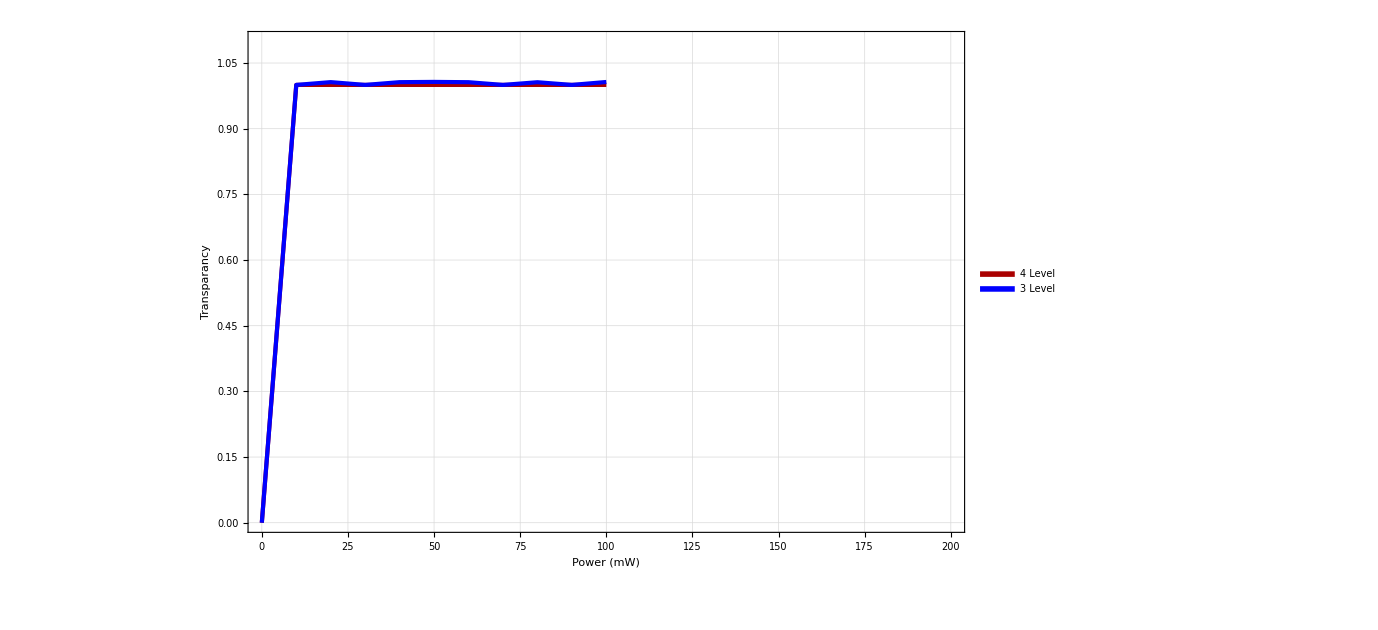

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.1}}]
```

γ=0.1

```mathematica
γ=0.1*5.750056;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,200,10}]
]
```

General::munfl: Exp[-713.172-383.04 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-730.088-361.543 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-746.068-339.005 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

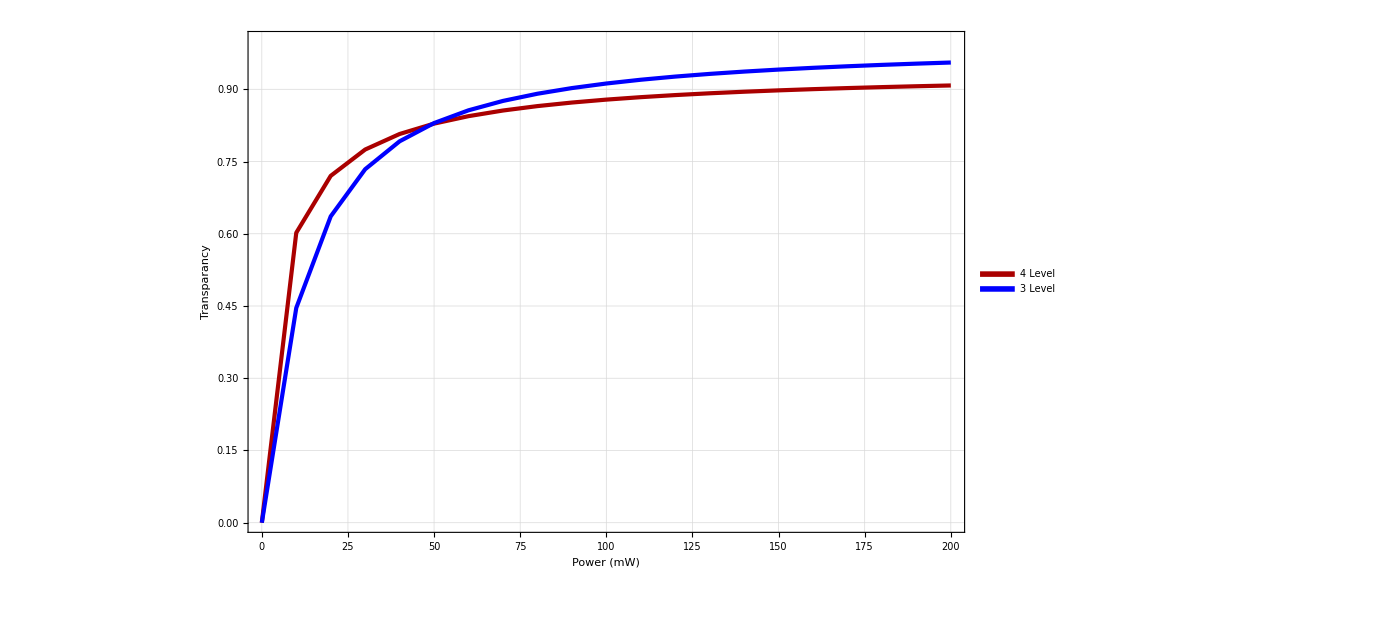

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.0}}]
```

γ=0.25

200

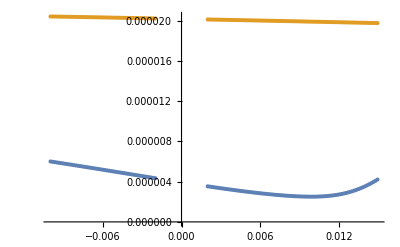

1.98755×10^-6

2.50932×10^-6

0.0000201971

0.0000199206

{-0.007,-0.00674,-0.00648,-0.00622,-0.00596,-0.0057,-0.00544,-0.00518,-0.00492,-0.00466,-0.0044,-0.00414,-0.00388,-0.00362,-0.00336,-0.0031,-0.00284,-0.00258,-0.00232,-0.00206,-0.0018,-0.00154,-0.00128,-0.00102,0.00106,0.00132,0.00158,0.00184,0.0021,0.00236,0.00262,0.00288,0.00314,0.0034,0.00366,0.00392,0.00418,0.00444,0.0047,0.00496,0.00522,0.00548,0.00574,0.006,0.00626,0.00652,0.00678}

```mathematica
p=200
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
ListPlot[{list3,list4}]
EIT=Min[DeleteCases[list[[All,2]],Indeterminate]]
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]]

ABS=list1[[Position[list,EIT][[1,1]]]][[2]]
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]]
```

```mathematica
γ=0.25*5.750056;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,200,2}]
]
```

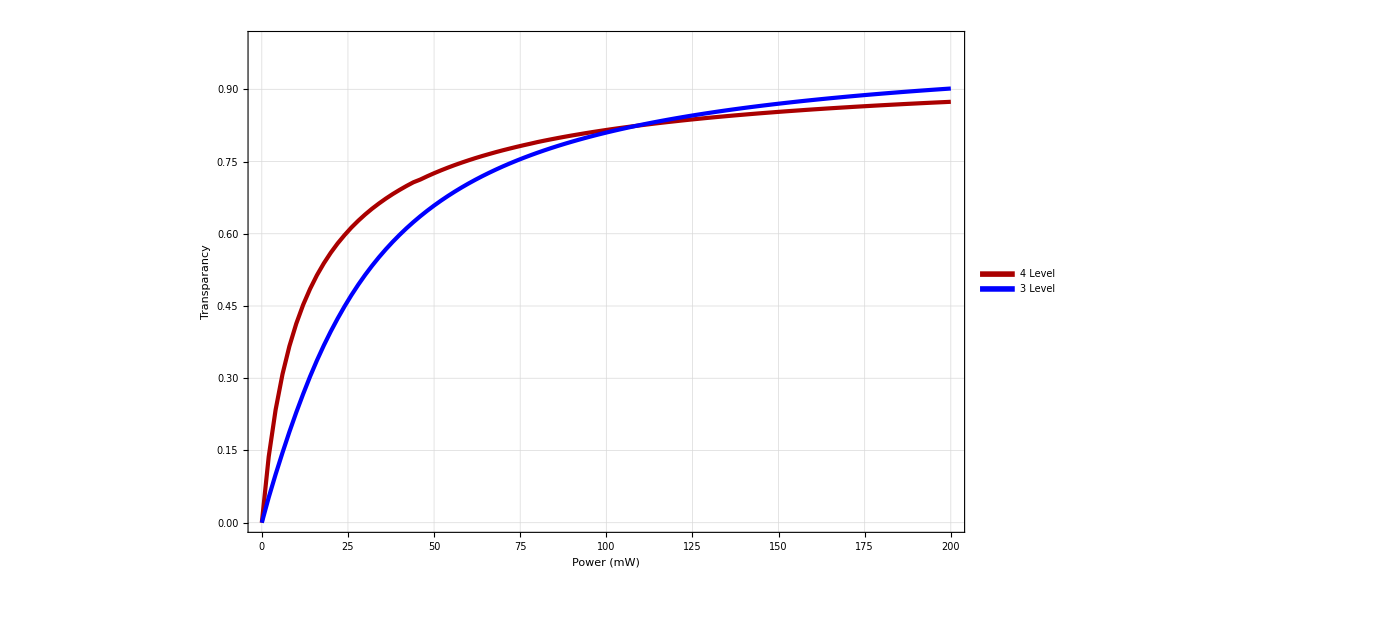

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
tp1=ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.0}}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure41U.eps",tp1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure41U.eps

γ=0.5

```mathematica
γ=0.5*5.750056;
TvP4[γ]={};TvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

TvP4[γ]=Append[TvP4[γ],{p,1-EIT1/ABS1}];
TvP3[γ]=Append[TvP3[γ],{p,1-EIT/ABS}];
,{p,0,100,10}]
]
```

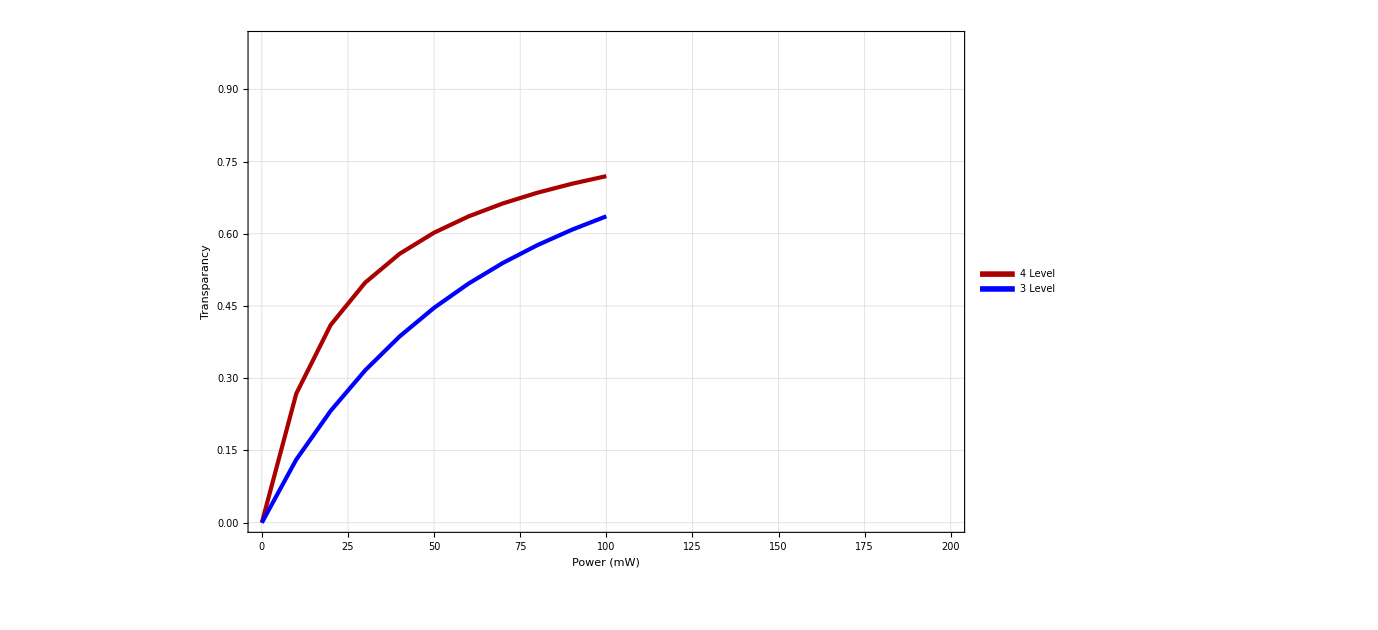

```mathematica
γ=0.5*5.750056;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{TvP4[γ],TvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,1.0}}]
```

## Trans vs decoherence

P=0γ

```mathematica
p=0;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

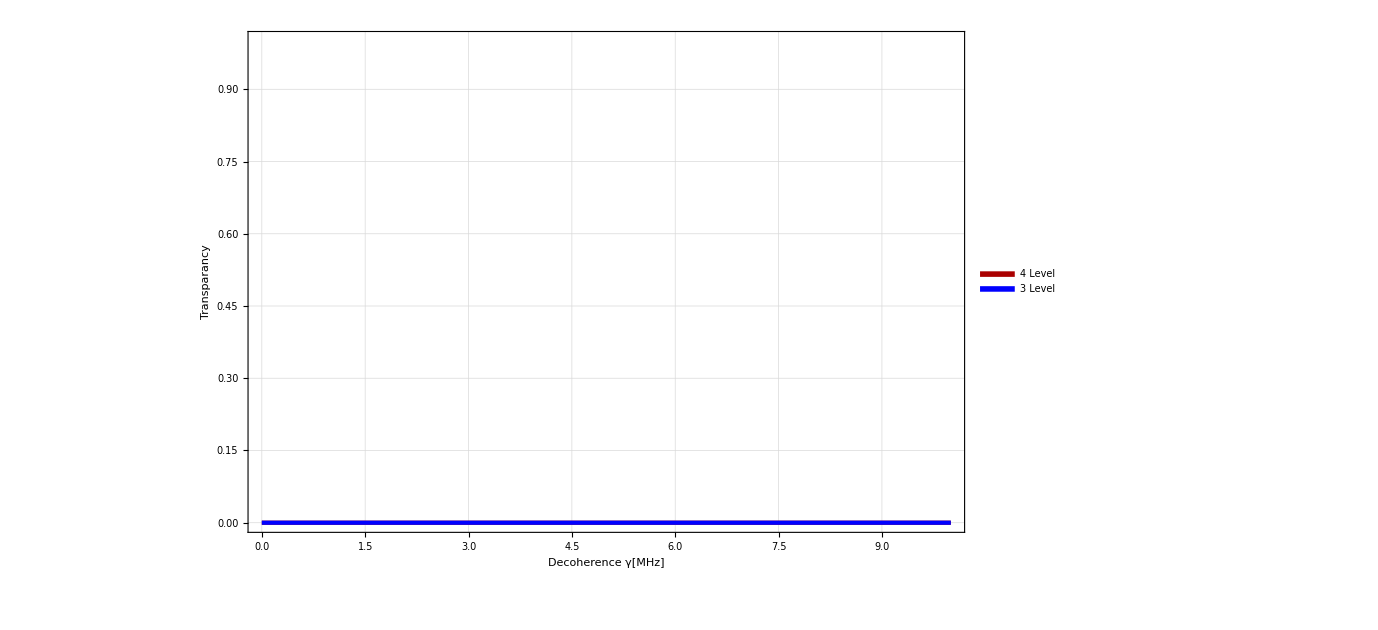

```mathematica
p=0;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.0}}]
```

P=2.5γ

```mathematica
p=3.99;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

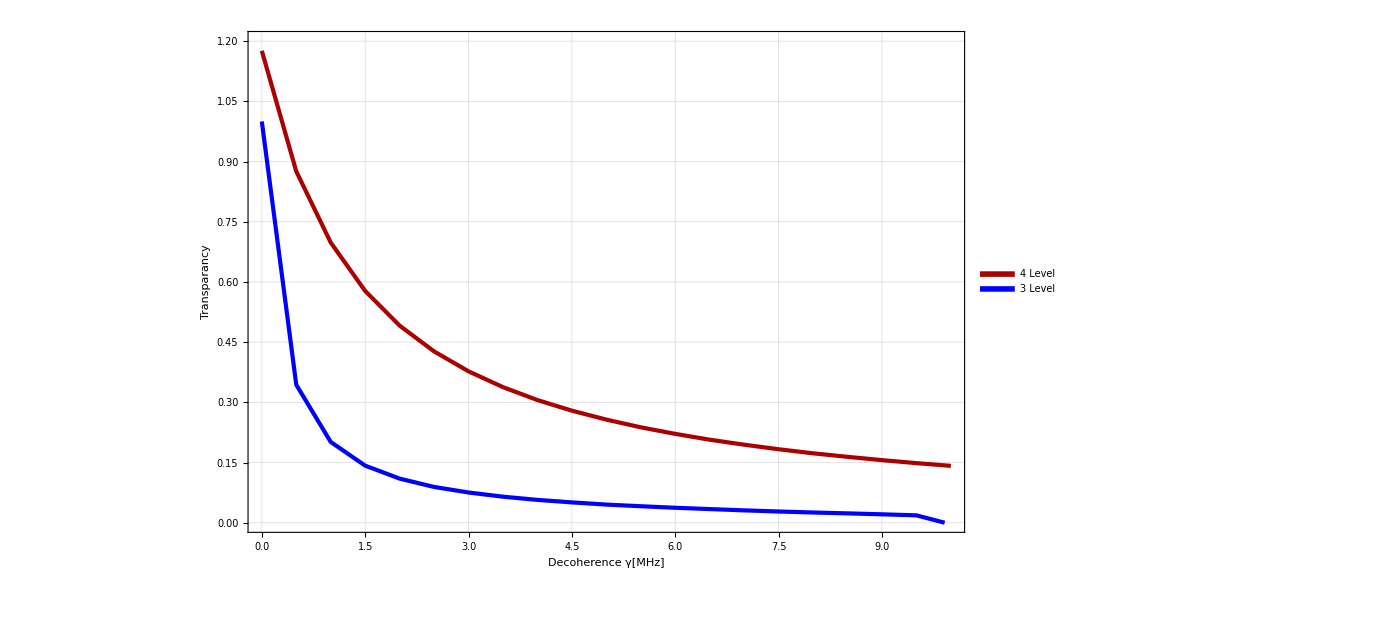

```mathematica
p=3.99;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.2}}]
```

P=5γ

```mathematica
p=15.8;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestscγ[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestscγ[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,3,0.01}]
]
```

```mathematica
nf1=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Tvγ4[p]
nf2=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Tvγ3[p]
```

{{0.,0.954574},{0.00173911,0.94669},{0.00347823,0.939004},{0.00521734,0.931548},{0.00695645,0.924325},{0.00869557,0.917282},{0.0104347,0.910416},{0.0121738,0.90377},{0.0139129,0.897282},{0.015652,0.890946},{0.0173911,0.884759},{0.0191302,0.878745},{0.0208694,0.872861},{0.0226085,0.867101},{0.0243476,0.86146},{0.0260867,0.855959},{0.0278258,0.850567},{0.0295649,0.845277},{0.031304,0.840084},{0.0330432,0.835007},{0.0347823,0.830021},{0.0365214,0.825119},{0.0382605,0.820301},{0.0399996,0.815581},{0.0417387,0.810935},{0.0434778,0.80636},{0.045217,0.801867},{0.0469561,0.797449},{0.0486952,0.793092},{0.0504343,0.788804},{0.0521734,0.784589},{0.0539125,0.780429},{0.0556516,0.776328},{0.0573907,0.772297},{0.0591299,0.768315},{0.060869,0.764387},{0.0626081,0.760523},{0.0643472,0.756704},{0.0660863,0.752935},{0.0678254,0.74919},{0.0695645,0.745469},{0.0713037,0.741773},{0.0730428,0.738102},{0.0747819,0.734455},{0.076521,0.730833},{0.0782601,0.727235},{0.0799992,0.723662},{0.0817383,0.720113},{0.0834774,0.716589},{0.0852166,0.713089},{0.0869557,0.709614},{0.0886948,0.706164},{0.0904339,0.702737},{0.092173,0.699336},{0.0939121,0.695958},{0.0956512,0.692604},{0.0973904,0.689275},{0.0991295,0.68597},{0.100869,0.682688},{0.102608,0.679431},{0.104347,0.676197},{0.106086,0.672987},{0.107825,0.6698},{0.109564,0.666636},{0.111303,0.663496},{0.113042,0.660379},{0.114781,0.657285},{0.116521,0.654214},{0.11826,0.651166},{0.119999,0.64814},{0.121738,0.645137},{0.123477,0.642156},{0.125216,0.639197},{0.126955,0.63626},{0.128694,0.633345},{0.130434,0.630452},{0.132173,0.627581},{0.133912,0.624731},{0.135651,0.621902},{0.13739,0.619094},{0.139129,0.616307},{0.140868,0.613541},{0.142607,0.610796},{0.144346,0.608071},{0.146086,0.605367},{0.147825,0.603309},{0.149564,0.601562},{0.151303,0.599819},{0.153042,0.598082},{0.154781,0.596349},{0.15652,0.59462},{0.158259,0.592897},{0.159998,0.591178},{0.161738,0.589465},{0.163477,0.587756},{0.165216,0.586052},{0.166955,0.584353},{0.168694,0.582659},{0.170433,0.58097},{0.172172,0.579287},{0.173911,0.577608},{0.17565,0.575934},{0.17739,0.574266},{0.179129,0.572602},{0.180868,0.570944},{0.182607,0.569291},{0.184346,0.567643},{0.186085,0.566},{0.187824,0.564363},{0.189563,0.56273},{0.191302,0.561103},{0.193042,0.559482},{0.194781,0.557865},{0.19652,0.556254},{0.198259,0.554648},{0.199998,0.553047},{0.201737,0.551452},{0.203476,0.549862},{0.205215,0.548278},{0.206955,0.546698},{0.208694,0.545125},{0.210433,0.543556},{0.212172,0.541993},{0.213911,0.540435},{0.21565,0.538883},{0.217389,0.537336},{0.219128,0.535794},{0.220867,0.534258},{0.222607,0.532727},{0.224346,0.531202},{0.226085,0.529682},{0.227824,0.528167},{0.229563,0.526658},{0.231302,0.525154},{0.233041,0.523656},{0.23478,0.522163},{0.236519,0.520675},{0.238259,0.519193},{0.239998,0.517717},{0.241737,0.516245},{0.243476,0.514779},{0.245215,0.513318},{0.246954,0.511863},{0.248693,0.510413},{0.250432,0.508969},{0.252171,0.50753},{0.253911,0.506096},{0.25565,0.504668},{0.257389,0.503245},{0.259128,0.501827},{0.260867,0.500414},{0.262606,0.499007},{0.264345,0.497606},{0.266084,0.496209},{0.267823,0.494818},{0.269563,0.493432},{0.271302,0.492063},{0.273041,0.490695},{0.27478,0.489342},{0.276519,0.487989},{0.278258,0.486642},{0.279997,0.485316},{0.281736,0.483985},{0.283476,0.482674},{0.285215,0.481359},{0.286954,0.480063},{0.288693,0.478764},{0.290432,0.477482},{0.292171,0.476198},{0.29391,0.47493},{0.295649,0.473661},{0.297388,0.472408},{0.299128,0.471153},{0.300867,0.469903},{0.302606,0.468673},{0.304345,0.467437},{0.306084,0.466221},{0.307823,0.464999},{0.309562,0.463796},{0.311301,0.462588},{0.31304,0.461397},{0.31478,0.460203},{0.316519,0.459024},{0.318258,0.457844},{0.319997,0.456667},{0.321736,0.45551},{0.323475,0.454346},{0.325214,0.453201},{0.326953,0.45205},{0.328692,0.450917},{0.330432,0.449779},{0.332171,0.448656},{0.33391,0.447531},{0.335649,0.446409},{0.337388,0.445306},{0.339127,0.444197},{0.340866,0.443105},{0.342605,0.442007},{0.344344,0.440926},{0.346084,0.43984},{0.347823,0.43877},{0.349562,0.437695},{0.351301,0.436624},{0.35304,0.435572},{0.354779,0.434512},{0.356518,0.43347},{0.358257,0.432422},{0.359996,0.431389},{0.361736,0.430352},{0.363475,0.429318},{0.365214,0.428302},{0.366953,0.427279},{0.368692,0.426273},{0.370431,0.42526},{0.37217,0.424263},{0.373909,0.423261},{0.375649,0.422262},{0.377388,0.421281},{0.379127,0.420292},{0.380866,0.41932},{0.382605,0.418341},{0.384344,0.417378},{0.386083,0.416409},{0.387822,0.415443},{0.389561,0.414495},{0.391301,0.413539},{0.39304,0.412586},{0.394779,0.411636},{0.396518,0.410689},{0.398257,0.409745},{0.399996,0.408804},{0.401735,0.407937},{0.403474,0.407018},{0.405213,0.406103},{0.406953,0.40519},{0.408692,0.40428},{0.410431,0.403372},{0.41217,0.402468},{0.413909,0.401567},{0.415648,0.400668},{0.417387,0.399772},{0.419126,0.398879},{0.420865,0.397989},{0.422605,0.397102},{0.424344,0.396217},{0.426083,0.395335},{0.427822,0.394456},{0.429561,0.39358},{0.4313,0.392707},{0.433039,0.391977},{0.434778,0.391138},{0.436517,0.3903},{0.438257,0.389465},{0.439996,0.388633},{0.441735,0.387803},{0.443474,0.386976},{0.445213,0.386151},{0.446952,0.385328},{0.448691,0.384508},{0.45043,0.38369},{0.45217,0.382875},{0.453909,0.382063},{0.455648,0.381252},{0.457387,0.380445},{0.459126,0.379639},{0.460865,0.378836},{0.462604,0.378036},{0.464343,0.377238},{0.466082,0.376442},{0.467822,0.375648},{0.469561,0.374858},{0.4713,0.374069},{0.473039,0.373283},{0.474778,0.372499},{0.476517,0.371866},{0.478256,0.37111},{0.479995,0.370357},{0.481734,0.369606},{0.483474,0.368856},{0.485213,0.368109},{0.486952,0.367364},{0.488691,0.366622},{0.49043,0.365881},{0.492169,0.365142},{0.493908,0.364406},{0.495647,0.363672},{0.497386,0.362939},{0.499126,0.362209},{0.500865,0.361481},{0.502604,0.360755},{0.504343,0.360031},{0.506082,0.35931},{0.507821,0.35859},{0.50956,0.357872},{0.511299,0.357157},{0.513038,0.356443},{0.514778,0.355732},{0.516517,0.355023},{0.518256,0.354315},{0.519995,0.353751},{0.521734,0.353068}}

{{0.,0.999984},{0.00173911,0.992765},{0.00347823,0.985554},{0.00521734,0.973228},{0.00695645,0.964341},{0.00869557,0.955479},{0.0104347,0.946647},{0.0121738,0.93785},{0.0139129,0.929093},{0.015652,0.920381},{0.0173911,0.911717},{0.0191302,0.903107},{0.0208694,0.894554},{0.0226085,0.886061},{0.0243476,0.877632},{0.0260867,0.86927},{0.0278258,0.860977},{0.0295649,0.852755},{0.031304,0.844607},{0.0330432,0.836535},{0.0347823,0.828587},{0.0365214,0.82083},{0.0382605,0.813162},{0.0399996,0.805583},{0.0417387,0.798094},{0.0434778,0.790694},{0.045217,0.783383},{0.0469561,0.77616},{0.0486952,0.769025},{0.0504343,0.761978},{0.0521734,0.755017},{0.0539125,0.748142},{0.0556516,0.741353},{0.0573907,0.734648},{0.0591299,0.728027},{0.060869,0.721488},{0.0626081,0.715032},{0.0643472,0.708656},{0.0660863,0.702361},{0.0678254,0.696144},{0.0695645,0.690006},{0.0713037,0.683945},{0.0730428,0.67796},{0.0747819,0.672051},{0.076521,0.666215},{0.0782601,0.660453},{0.0799992,0.654763},{0.0817383,0.649145},{0.0834774,0.643596},{0.0852166,0.638117},{0.0869557,0.632707},{0.0886948,0.627363},{0.0904339,0.622086},{0.092173,0.616875},{0.0939121,0.611728},{0.0956512,0.606644},{0.0973904,0.601624},{0.0991295,0.596665},{0.100869,0.591767},{0.102608,0.586929},{0.104347,0.58215},{0.106086,0.577429},{0.107825,0.572765},{0.109564,0.568159},{0.111303,0.563608},{0.113042,0.559111},{0.114781,0.554669},{0.116521,0.55028},{0.11826,0.545944},{0.119999,0.541659},{0.121738,0.537426},{0.123477,0.533242},{0.125216,0.529108},{0.126955,0.525023},{0.128694,0.520986},{0.130434,0.516996},{0.132173,0.513053},{0.133912,0.509156},{0.135651,0.505304},{0.13739,0.501496},{0.139129,0.497733},{0.140868,0.494013},{0.142607,0.490336},{0.144346,0.4867},{0.146086,0.483107},{0.147825,0.479554},{0.149564,0.476041},{0.151303,0.472791},{0.153042,0.469557},{0.154781,0.466356},{0.15652,0.463189},{0.158259,0.460055},{0.159998,0.456953},{0.161738,0.453883},{0.163477,0.450845},{0.165216,0.447838},{0.166955,0.444862},{0.168694,0.441916},{0.170433,0.439},{0.172172,0.436113},{0.173911,0.433256},{0.17565,0.430427},{0.17739,0.427627},{0.179129,0.424855},{0.180868,0.42211},{0.182607,0.419393},{0.184346,0.416702},{0.186085,0.414039},{0.187824,0.411401},{0.189563,0.40879},{0.191302,0.406204},{0.193042,0.403643},{0.194781,0.401107},{0.19652,0.398596},{0.198259,0.39611},{0.199998,0.393647},{0.201737,0.391208},{0.203476,0.388792},{0.205215,0.3864},{0.206955,0.38403},{0.208694,0.381683},{0.210433,0.379359},{0.212172,0.377056},{0.213911,0.374775},{0.21565,0.372516},{0.217389,0.370278},{0.219128,0.36806},{0.220867,0.365864},{0.222607,0.363831},{0.224346,0.361803},{0.226085,0.359792},{0.227824,0.357799},{0.229563,0.355822},{0.231302,0.353861},{0.233041,0.351917},{0.23478,0.349989},{0.236519,0.348077},{0.238259,0.346181},{0.239998,0.344301},{0.241737,0.342436},{0.243476,0.340587},{0.245215,0.338753},{0.246954,0.336934},{0.248693,0.33513},{0.250432,0.33334},{0.252171,0.331565},{0.253911,0.329805},{0.25565,0.328059},{0.257389,0.326327},{0.259128,0.324609},{0.260867,0.322906},{0.262606,0.321215},{0.264345,0.319539},{0.266084,0.317876},{0.267823,0.316226},{0.269563,0.314589},{0.271302,0.312966},{0.273041,0.311355},{0.27478,0.309757},{0.276519,0.308172},{0.278258,0.306599},{0.279997,0.305039},{0.281736,0.303491},{0.283476,0.301955},{0.285215,0.300656},{0.286954,0.299229},{0.288693,0.297812},{0.290432,0.296405},{0.292171,0.295008},{0.29391,0.293621},{0.295649,0.292244},{0.297388,0.290876},{0.299128,0.289518},{0.300867,0.288169},{0.302606,0.28683},{0.304345,0.285501},{0.306084,0.28418},{0.307823,0.282869},{0.309562,0.281567},{0.311301,0.280274},{0.31304,0.278989},{0.31478,0.277714},{0.316519,0.276448},{0.318258,0.27519},{0.319997,0.273941},{0.321736,0.272701},{0.323475,0.271469},{0.325214,0.270246},{0.326953,0.269031},{0.328692,0.267824},{0.330432,0.266626},{0.332171,0.265436},{0.33391,0.264254},{0.335649,0.26308},{0.337388,0.261914},{0.339127,0.260911},{0.340866,0.259822},{0.342605,0.25874},{0.344344,0.257664},{0.346084,0.256595},{0.347823,0.255532},{0.349562,0.254476},{0.351301,0.253426},{0.35304,0.252383},{0.354779,0.251346},{0.356518,0.250315},{0.358257,0.249291},{0.359996,0.248273},{0.361736,0.247261},{0.363475,0.246255},{0.365214,0.245256},{0.366953,0.244262},{0.368692,0.243275},{0.370431,0.242293},{0.37217,0.241317},{0.373909,0.240348},{0.375649,0.239384},{0.377388,0.238426},{0.379127,0.237473},{0.380866,0.236527},{0.382605,0.235586},{0.384344,0.23465},{0.386083,0.233721},{0.387822,0.232797},{0.389561,0.231878},{0.391301,0.231132},{0.39304,0.230269},{0.394779,0.229411},{0.396518,0.228558},{0.398257,0.227709},{0.399996,0.226865},{0.401735,0.226025},{0.403474,0.22519},{0.405213,0.22436},{0.406953,0.223534},{0.408692,0.222712},{0.410431,0.221895},{0.41217,0.221082},{0.413909,0.220274},{0.415648,0.21947},{0.417387,0.21867},{0.419126,0.217875},{0.420865,0.217084},{0.422605,0.216297},{0.424344,0.215515},{0.426083,0.214736},{0.427822,0.213962},{0.429561,0.213192},{0.4313,0.212426},{0.433039,0.211664},{0.434778,0.210907},{0.436517,0.210153},{0.438257,0.209403},{0.439996,0.208658},{0.441735,0.208102},{0.443474,0.207398},{0.445213,0.206698},{0.446952,0.206001},{0.448691,0.205307},{0.45043,0.204617},{0.45217,0.20393},{0.453909,0.203247},{0.455648,0.202566},{0.457387,0.20189},{0.459126,0.201216},{0.460865,0.200546},{0.462604,0.199879},{0.464343,0.199215},{0.466082,0.198554},{0.467822,0.197897},{0.469561,0.197243},{0.4713,0.196592},{0.473039,0.195944},{0.474778,0.195299},{0.476517,0.194657},{0.478256,0.194019},{0.479995,0.193383},{0.481734,0.192751},{0.483474,0.192122},{0.485213,0.191495},{0.486952,0.190872},{0.488691,0.19042},{0.49043,0.18983},{0.492169,0.189242},{0.493908,0.188656},{0.495647,0.188074},{0.497386,0.187493},{0.499126,0.186916},{0.500865,0.186341},{0.502604,0.185768},{0.504343,0.185198},{0.506082,0.18463},{0.507821,0.184065},{0.50956,0.183503},{0.511299,0.182943},{0.513038,0.182385},{0.514778,0.18183},{0.516517,0.181277},{0.518256,0.180727},{0.519995,0.180179},{0.521734,0.179634}}

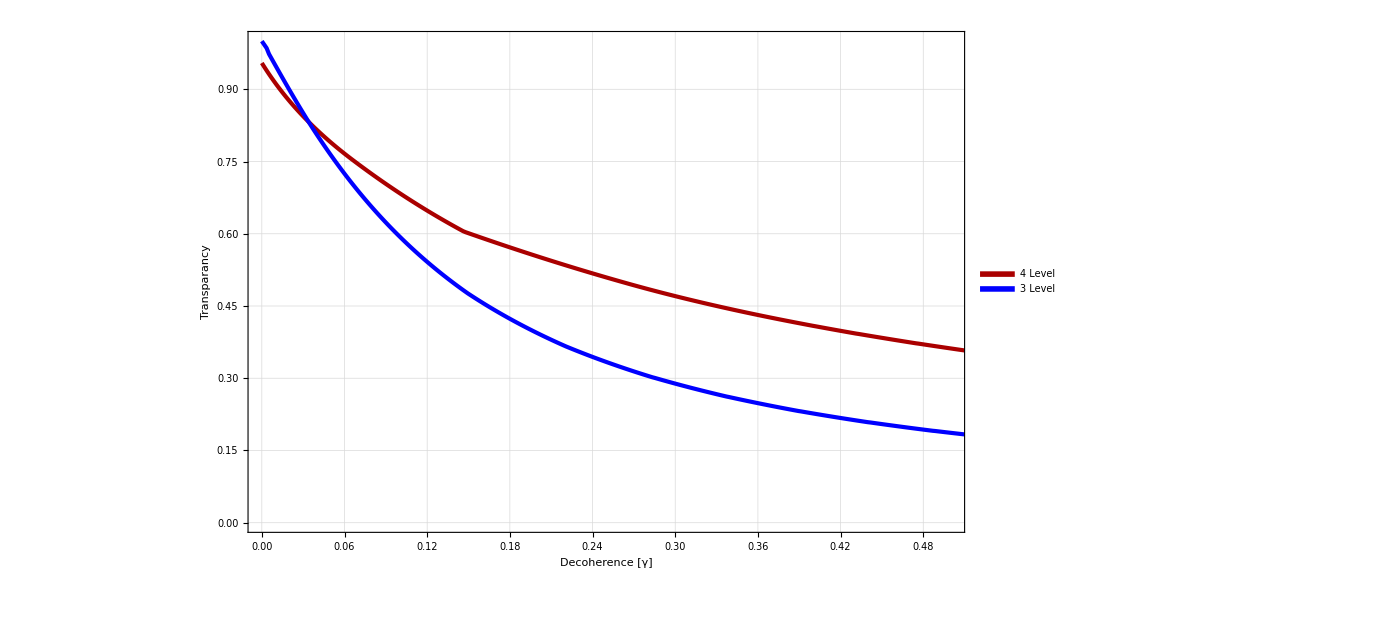

```mathematica
p=15.8;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
td1=ListPlot[{nf1,nf2},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.8}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence [γ]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,0.5},{0.0,1.0}}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure42U.eps",td1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure42U.eps

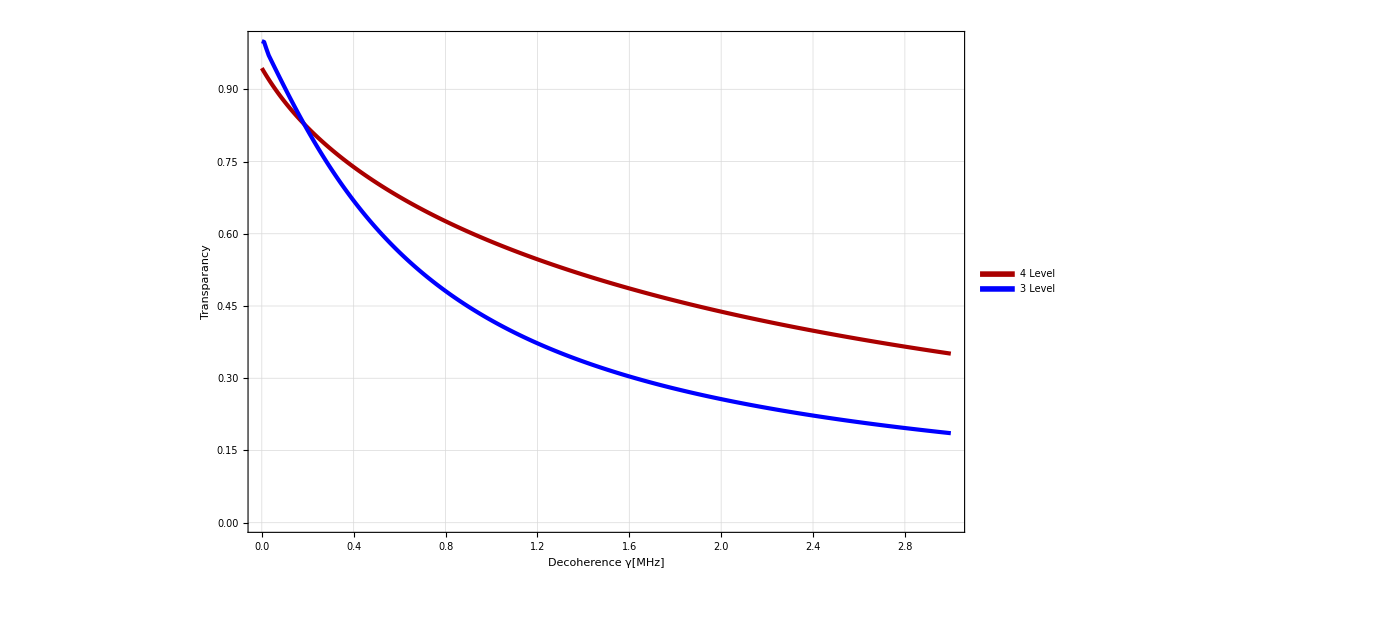

```mathematica
p=15.8;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
td1=ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.8}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,3},{0,1.0}}]
```

P=10γ

```mathematica
p=65;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

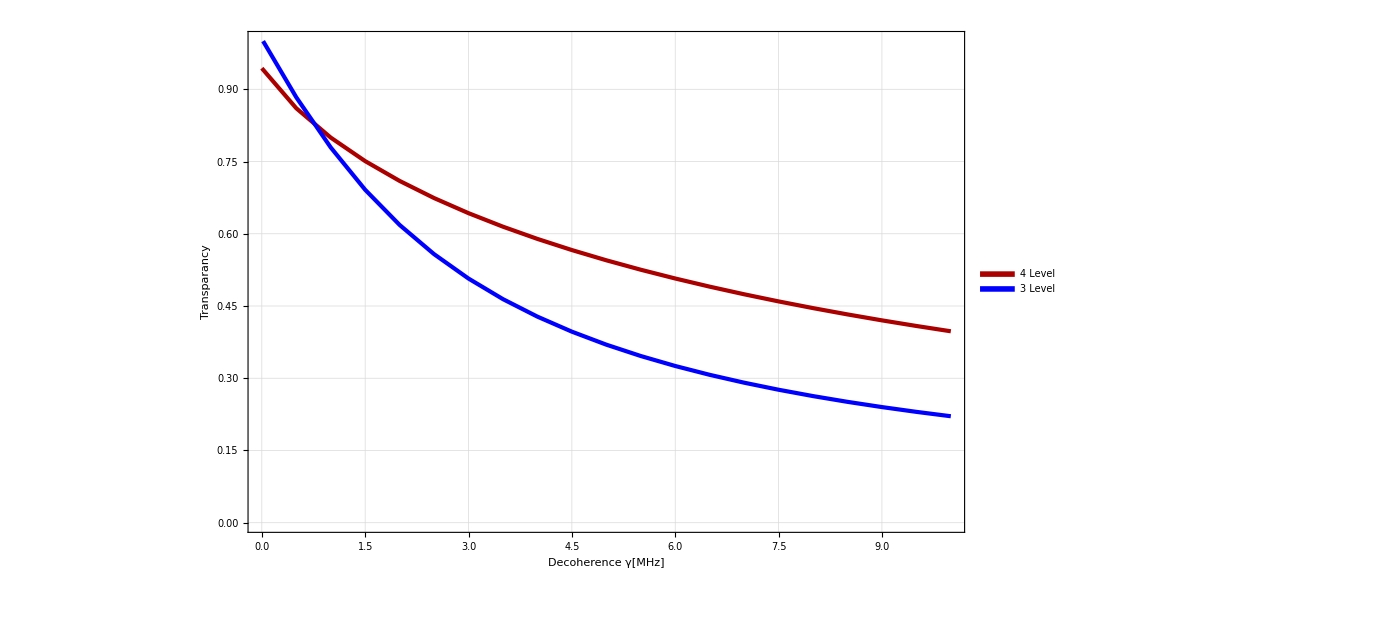

```mathematica
p=65;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.0}}]
```

P=15γ

```mathematica
p=142.75;
Tvγ4[p]={};Tvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
list=Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev3DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev4DoppTestsc[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];

ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

Tvγ4[p]=Append[Tvγ4[p],{γ,1-EIT1/ABS1}];
Tvγ3[p]=Append[Tvγ3[p],{γ,1-EIT/ABS}];
,{γ,0,10,0.5}]
]
```

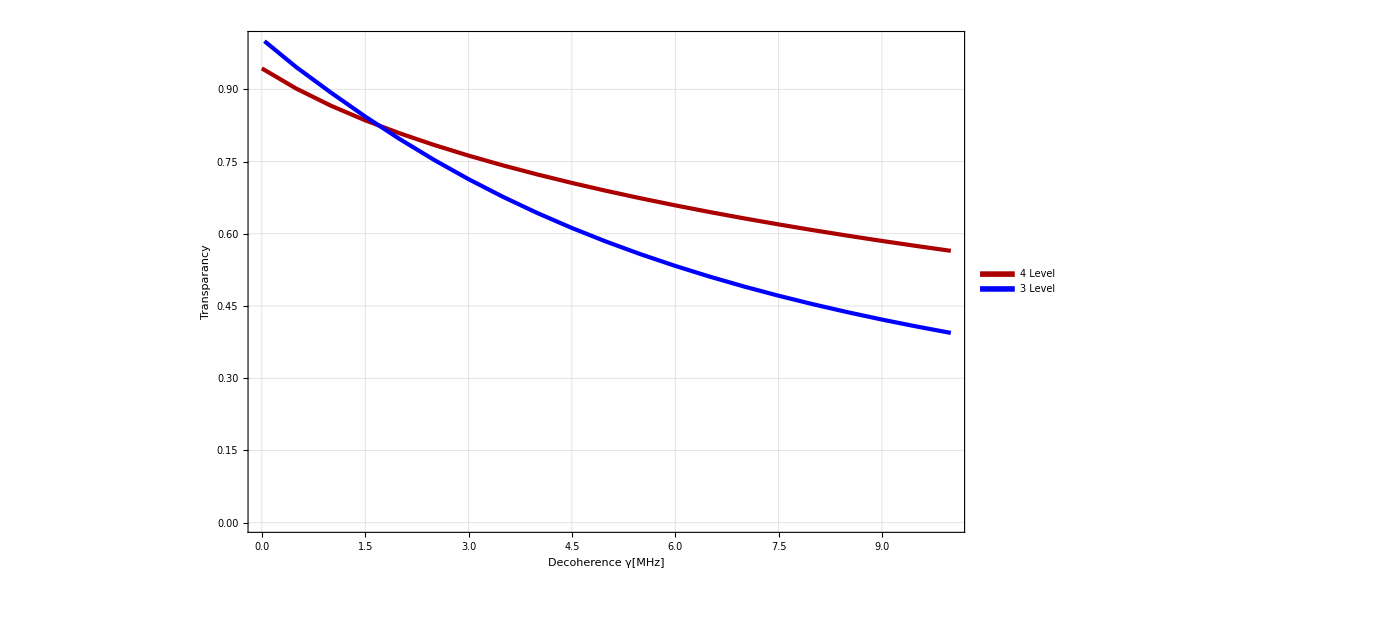

```mathematica
p=142.75;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
ListPlot[{Tvγ4[p],Tvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1.0}}]
```

## FWHM vs power

γ=0

```mathematica
γ=0*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.004&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.002&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,3,200,25}]
]
```

Part::partw: Part 2 of {{{-0.00063,9.83952×10^-6},{-0.00062,9.74711×10^-6},{-0.00061,9.65333×10^-6},{-0.0006,9.55816×10^-6},{-0.00059,9.46162×10^-6},{-0.00058,9.36372×10^-6},{-0.00057,9.26447×10^-6},{0.00029,9.66721×10^-6}}} does not exist.

Part::partd: Part specification {{{-0.00063,9.83952×10^-6},{-0.00062,9.74711×10^-6},{-0.00061,9.65333×10^-6},{-0.0006,9.55816×10^-6},{-0.00059,9.46162×10^-6},{-0.00058,9.36372×10^-6},{-0.00057,9.26447×10^-6},{0.00029,9.66721×10^-6}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.00016,9.13636×10^-6},{0.00014,8.9964×10^-6}}} does not exist.

Part::partd: Part specification {{{-0.00016,9.13636×10^-6},{0.00014,8.9964×10^-6}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

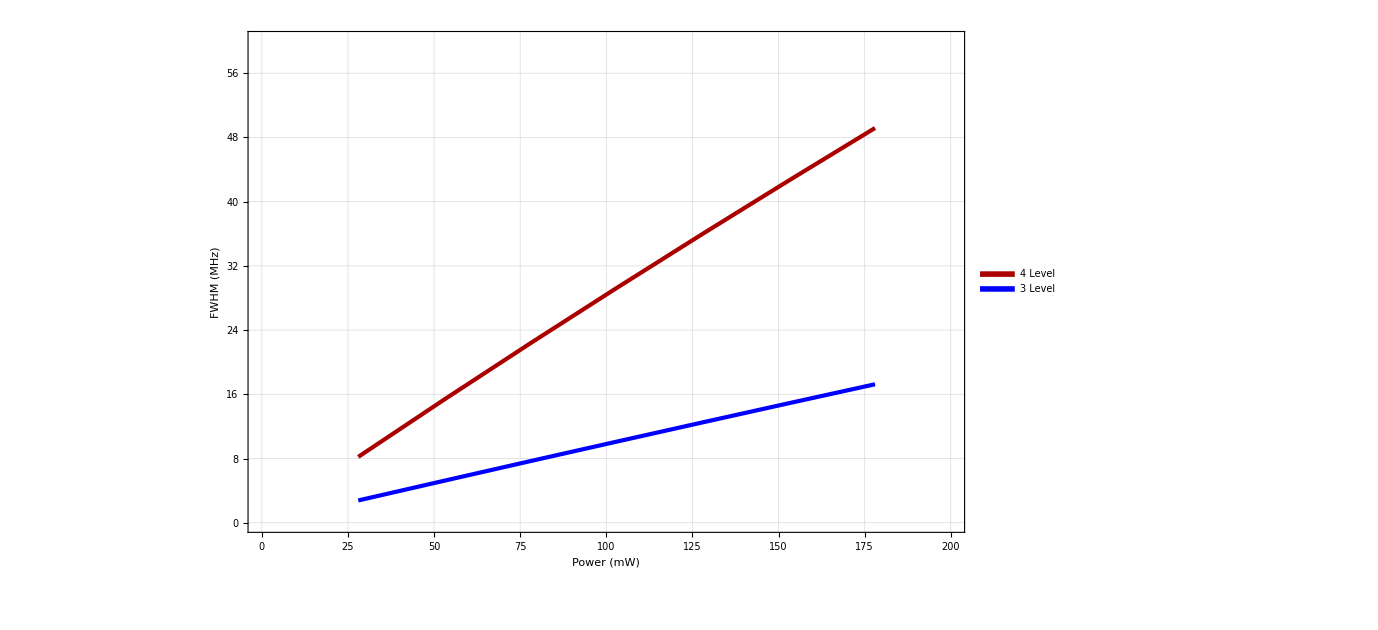

```mathematica
ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,60}}]
```

γ=0.1

```mathematica
γ=0.1*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.004&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,3,200,15}]
]
```

Part::partw: Part 2 of {{{-0.00197,0.0000150675},{-0.00196,0.0000150538},{-0.00195,0.00001504},{-0.00194,0.000015026},{-0.00193,0.000015012},{-0.00192,0.0000149979},{-0.00191,0.0000149836},{-0.0019,0.0000149693},{-0.00189,0.0000149548},{-0.00188,0.0000149403},{-0.00187,0.0000149256},{-0.00186,0.0000149109},{-0.00185,0.000014896},{-0.00184,0.000014881},{-0.00183,0.000014866},{-0.00182,0.0000148508},{-0.00181,0.0000148355},{0.00039,0.0000148753},{0.0004,0.0000149572},{0.00041,0.0000150391}}} does not exist.

Part::partd: Part specification {{{-0.00197,0.0000150675},{-0.00196,0.0000150538},{-0.00195,0.00001504},{-0.00194,0.000015026},{-0.00193,0.000015012},{-0.00192,0.0000149979},{-0.00191,0.0000149836},{-0.0019,0.0000149693},{-0.00189,0.0000149548},{-0.00188,0.0000149403},{-0.00187,0.0000149256},{-0.00186,0.0000149109},{-0.00185,0.000014896},{-0.00184,0.000014881},{-0.00183,0.000014866},{-0.00182,0.0000148508},{-0.00181,0.0000148355},{0.00039,0.0000148753},{0.0004,0.0000149572},{0.00041,0.0000150391}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.0017,0.0000165016},{-0.00169,0.0000164936},{-0.00168,0.0000164856},{-0.00167,0.0000164775},{-0.00166,0.0000164693},{-0.00165,0.0000164611},{-0.00164,0.0000164528},{-0.00163,0.0000164444},{-0.00162,0.000016436},{-0.00161,0.0000164275},{-0.0016,0.0000164189},{-0.00159,0.0000164103},{-0.00158,0.0000164016},{-0.00157,0.0000163928},{-0.00156,0.000016384},{-0.00155,0.0000163751},{0.00023,0.0000163781},{0.00024,0.0000164384},{0.00025,0.0000164988}}} does not exist.

Part::partd: Part specification {{{-0.0017,0.0000165016},{-0.00169,0.0000164936},{-0.00168,0.0000164856},{-0.00167,0.0000164775},{-0.00166,0.0000164693},{-0.00165,0.0000164611},{-0.00164,0.0000164528},{-0.00163,0.0000164444},{-0.00162,0.000016436},{-0.00161,0.0000164275},{-0.0016,0.0000164189},{-0.00159,0.0000164103},{-0.00158,0.0000164016},{-0.00157,0.0000163928},{-0.00156,0.000016384},{-0.00155,0.0000163751},{0.00023,0.0000163781},{0.00024,0.0000164384},{0.00025,0.0000164988}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

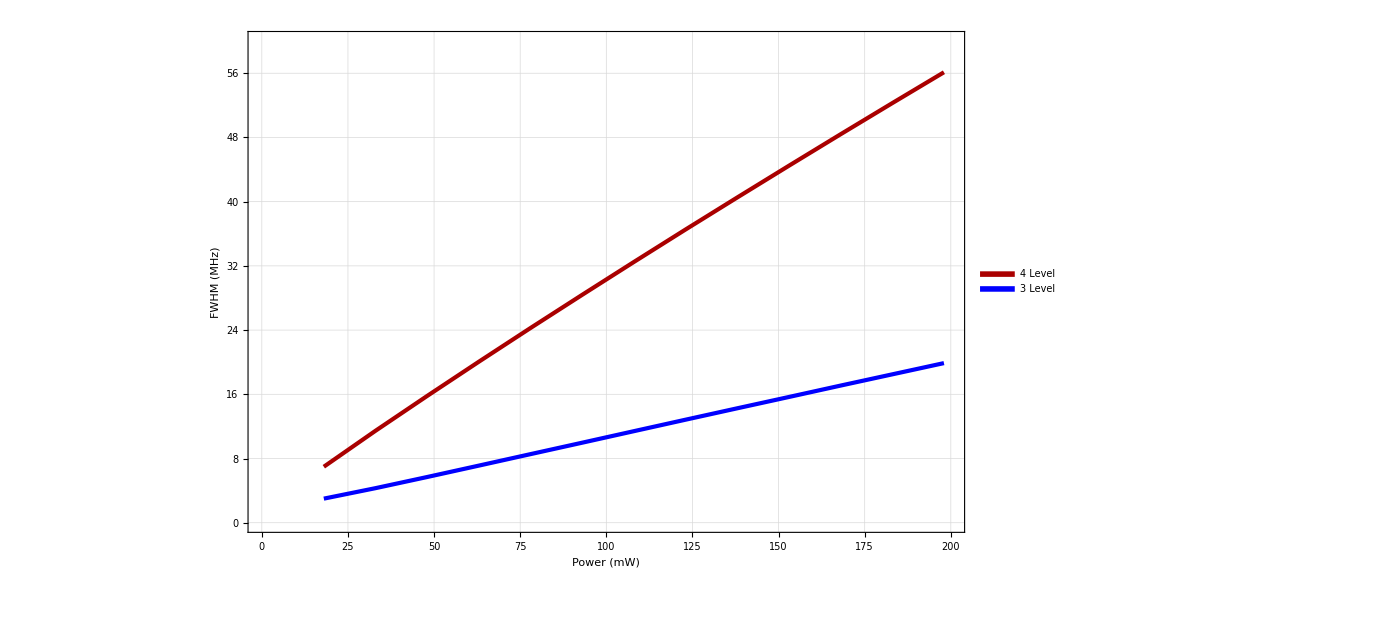

```mathematica
ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,60}}]
```

γ=0.25

80

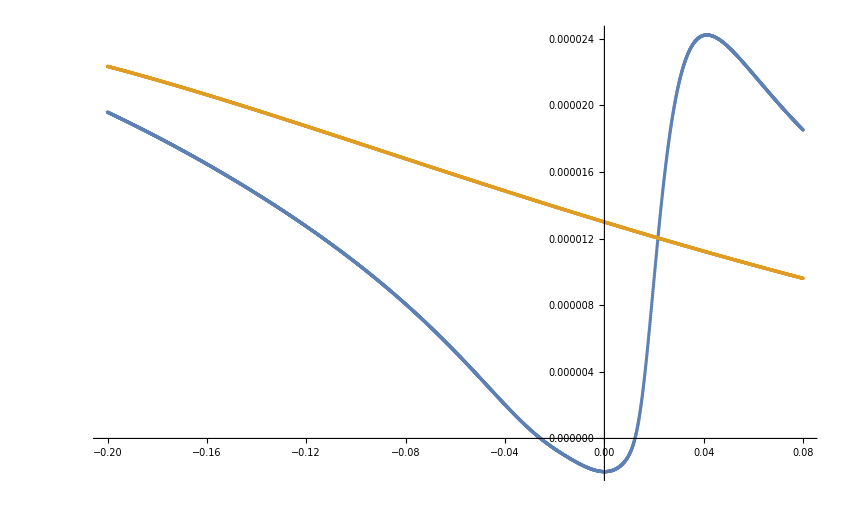

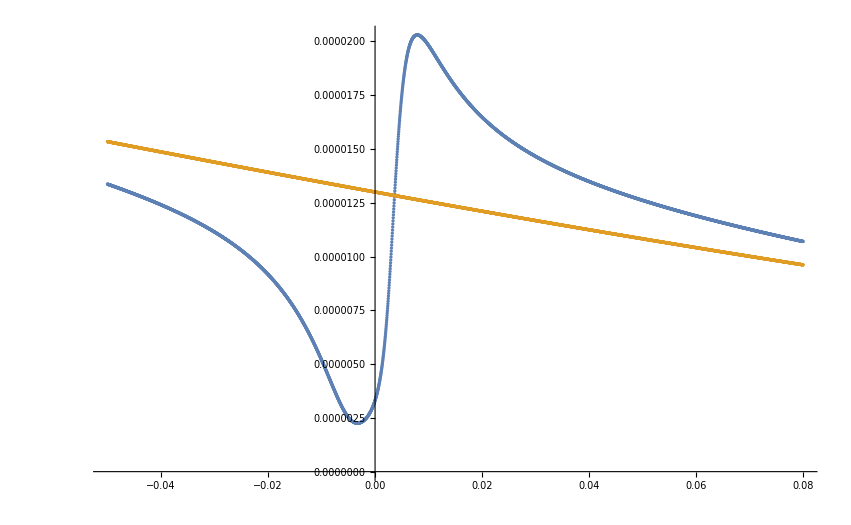

```mathematica
γ=0.25*5.750056;
p=80
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
ListPlot[{list,list1},PlotRange->All]
ListPlot[{list3,list4},PlotRange->All]
```

```mathematica
Lev4DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=If[P≥ 80/1000,
Select[Range[-0.20,0.05,0.000083],#≥ 0.0015∨#≤ -0.0015&]*10^9,
Range[-0.20,0.08,0.000083]*10^9];
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
γ=0.25*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
If[p<10,
list=Select[Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.015&];
list1=Select[Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.015&];
list3=Select[Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.005&];
list4=Select[Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.005&];,
list=Select[Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.05&];
list1=Select[Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.05&];
list3=Select[Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0],#[[1]]<0.02&];
list4=Select[Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0],#[[1]]<0.02&];
];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0025&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[-1]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0025&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[-1]][[All,1]]]]}];
,{p,3,200,2}]
]
```

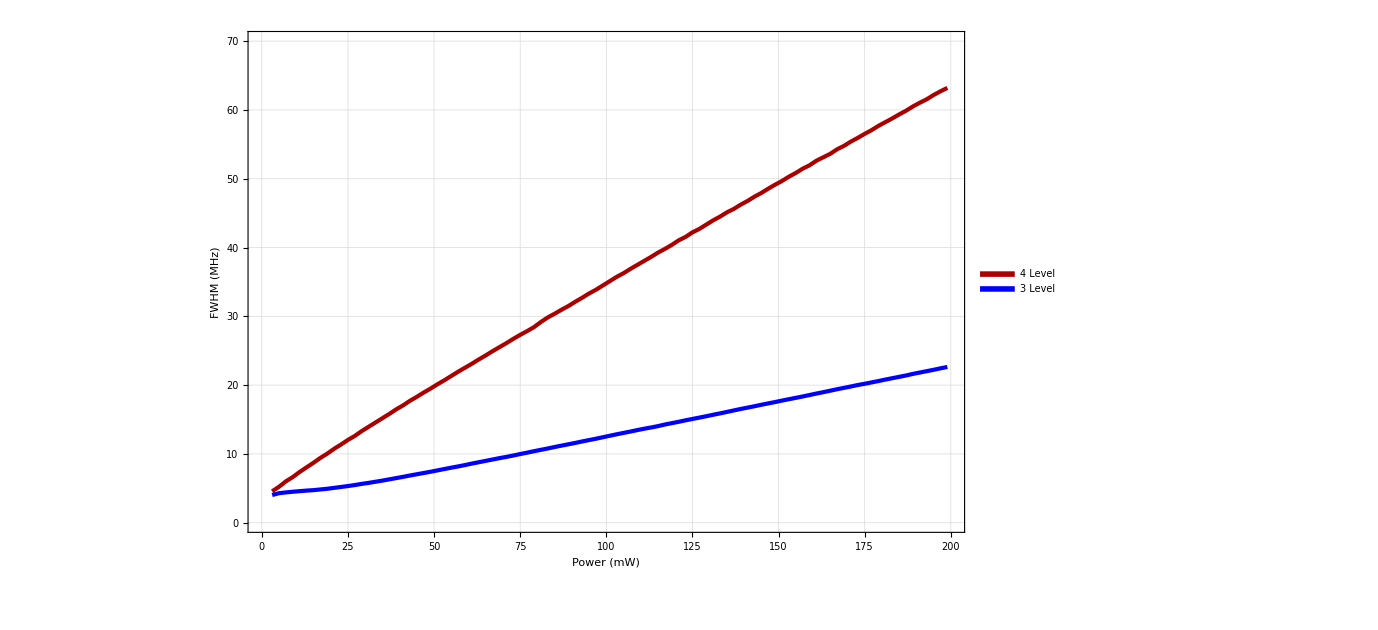

```mathematica
Fp1=ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,70}}]
```

```mathematica
Hey[list_]:=Transpose[{(Ome[list[[All,1]]/1000,1/1000]/(2 π 5.750056 10^6))^2,list⟦All,2⟧}]
```

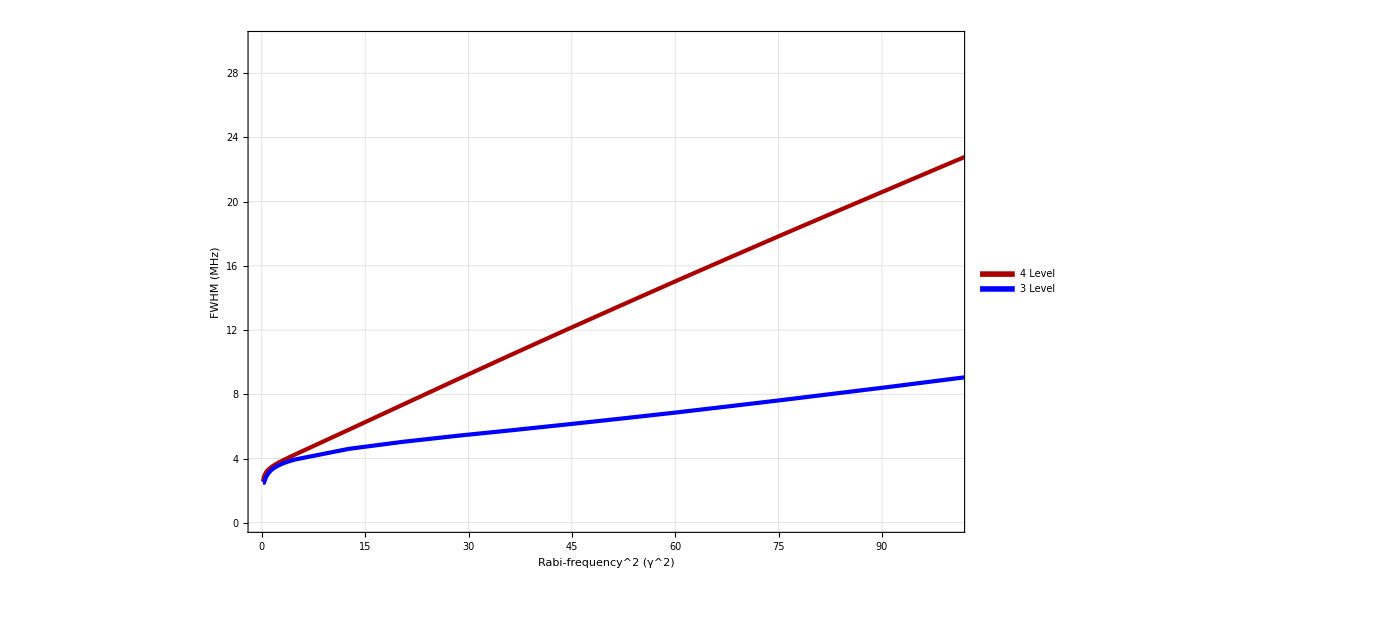

```mathematica
Fp1=ListPlot[{Hey[FvP4[γ]],Hey[FvP3[γ]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Rabi-frequency^2 Ω(γ^2)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,100},{0,30}}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure43U.eps",Fp1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure43U.eps

γ=1

```mathematica
γ=1*5.750056;
FvP4[γ]={};FvP3[γ]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc3[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc3[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc3[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc3[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0015&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0015&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,1.5,25,2}]
]

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.004&];
FvP4[γ]=Append[FvP4[γ],{p,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
FvP3[γ]=Append[FvP3[γ],{p,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{p,25,200,25}]
]
```

Part::partw: Part 2 of {{{-0.00318,0.0000129368},{-0.00317,0.0000129364},{-0.00316,0.0000129361},{-0.00315,0.0000129357},{-0.00314,0.0000129354},{-0.00313,0.0000129351},{-0.00312,0.0000129347},{-0.00311,0.0000129344},{-0.0031,0.0000129341}}} does not exist.

Part::partd: Part specification {{{-0.00318,0.0000129368},{-0.00317,0.0000129364},{-0.00316,0.0000129361},{-0.00315,0.0000129357},{-0.00314,0.0000129354},{-0.00313,0.0000129351},{-0.00312,0.0000129347},{-0.00311,0.0000129344},{-0.0031,0.0000129341}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

$Aborted

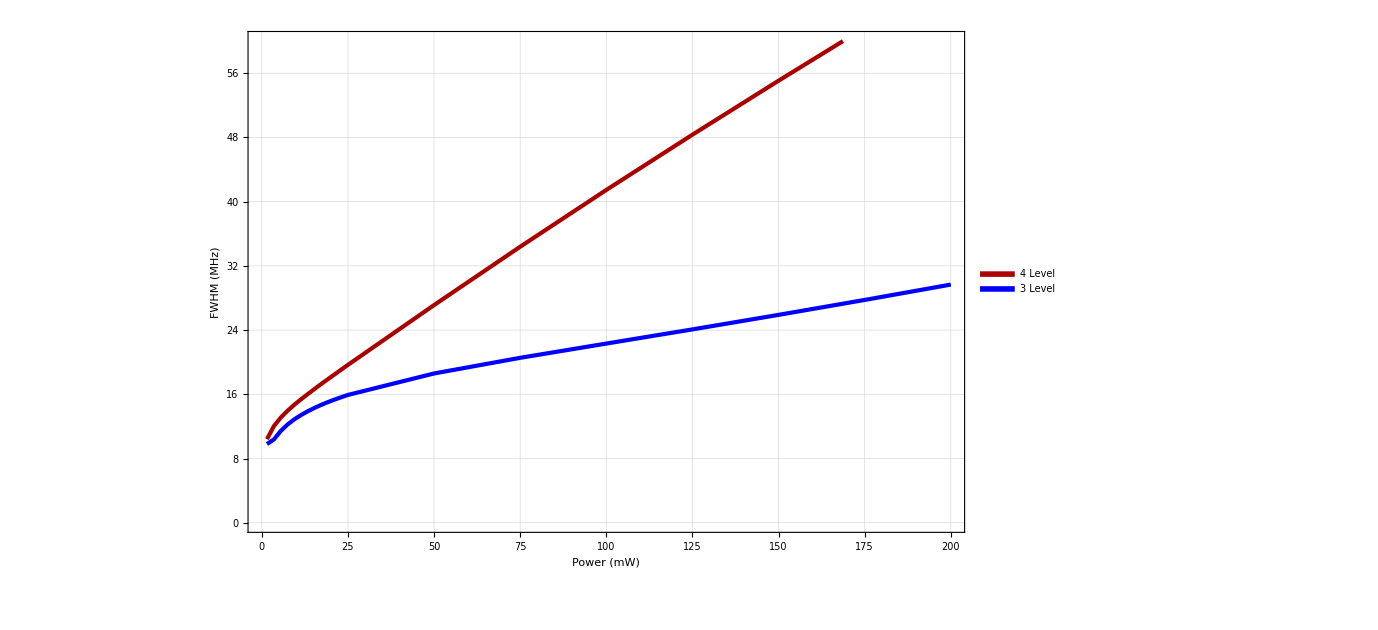

```mathematica
ListPlot[{FvP4[γ],FvP3[γ]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,200},{0,60}}]
```

## FWHM vs dec

p=0

```mathematica
p=0;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.002&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.001&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

$Aborted

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,25}}]
```

-Graphics-

p=2.5

```mathematica
p=3.99;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc4[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc4[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc4[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc4[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0015&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0008&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

Part::partw: Part 2 of {{{-0.000844,9.88471×10^-6},{-0.000842,9.87098×10^-6},{-0.00084,9.85722×10^-6},{-0.000838,9.84343×10^-6},{-0.000836,9.82961×10^-6},{-0.000834,9.81576×10^-6},{-0.000832,9.80187×10^-6},{-0.00083,9.78796×10^-6},{-0.000828,9.77401×10^-6},{-0.000826,9.76004×10^-6},{-0.000824,9.74603×10^-6},«29»,{-0.000764,9.31132×10^-6},{-0.000762,9.29636×10^-6},{-0.00076,9.28136×10^-6},{-0.000758,9.26633×10^-6},{-0.000756,9.25128×10^-6},{-0.000754,9.23619×10^-6},{-0.000752,9.22107×10^-6},{0.00038,9.28893×10^-6},{0.000382,9.42374×10^-6},{0.000384,9.55804×10^-6},«2»}} does not exist.

Part::partd: Part specification {{{-0.000844,9.88471×10^-6},{-0.000842,9.87098×10^-6},{-0.00084,9.85722×10^-6},{-0.000838,9.84343×10^-6},{-0.000836,9.82961×10^-6},{-0.000834,9.81576×10^-6},{-0.000832,9.80187×10^-6},{-0.00083,9.78796×10^-6},{-0.000828,9.77401×10^-6},{-0.000826,9.76004×10^-6},{-0.000824,9.74603×10^-6},«29»,{-0.000764,9.31132×10^-6},{-0.000762,9.29636×10^-6},{-0.00076,9.28136×10^-6},{-0.000758,9.26633×10^-6},{-0.000756,9.25128×10^-6},{-0.000754,9.23619×10^-6},{-0.000752,9.22107×10^-6},{0.00038,9.28893×10^-6},{0.000382,9.42374×10^-6},{0.000384,9.55804×10^-6},«2»}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.00022,9.3729×10^-6},{-0.000218,9.30935×10^-6},{-0.000216,9.24449×10^-6},{-0.000214,9.17829×10^-6},{-0.000212,9.11071×10^-6},{-0.00021,9.04173×10^-6},{-0.000208,8.9713×10^-6},{-0.000206,8.8994×10^-6},{-0.000204,8.82599×10^-6},{-0.000202,8.75103×10^-6},{0.000184,8.81761×10^-6},{0.000186,8.98162×10^-6},{0.000188,9.14726×10^-6},{0.00019,9.31451×10^-6}}} does not exist.

Part::partd: Part specification {{{-0.00022,9.3729×10^-6},{-0.000218,9.30935×10^-6},{-0.000216,9.24449×10^-6},{-0.000214,9.17829×10^-6},{-0.000212,9.11071×10^-6},{-0.00021,9.04173×10^-6},{-0.000208,8.9713×10^-6},{-0.000206,8.8994×10^-6},{-0.000204,8.82599×10^-6},{-0.000202,8.75103×10^-6},{0.000184,8.81761×10^-6},{0.000186,8.98162×10^-6},{0.000188,9.14726×10^-6},{0.00019,9.31451×10^-6}}}⟦2⟧⟦All,1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{-0.010246,0.00001802},{-0.010244,0.0000180199},{-0.010242,0.0000180198},{-0.01024,0.0000180198},{-0.010238,0.0000180197},{-0.010236,0.0000180197},{-0.010234,0.0000180196},{-0.010232,0.0000180195},{-0.01023,0.0000180195},{-0.010228,0.0000180194},{-0.010226,0.0000180194},{-0.010224,0.0000180193},«27»,{-0.010168,0.0000180176},{-0.010166,0.0000180176},{-0.010164,0.0000180175},{-0.010162,0.0000180174},{-0.01016,0.0000180174},{-0.010158,0.0000180173},{-0.010156,0.0000180172},{-0.010154,0.0000180172},{-0.010152,0.0000180171},{-0.01015,0.0000180171},{-0.010148,0.000018017},«141»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {{{-0.010246,0.00001802},{-0.010244,0.0000180199},{-0.010242,0.0000180198},{-0.01024,0.0000180198},{-0.010238,0.0000180197},{-0.010236,0.0000180197},{-0.010234,0.0000180196},{-0.010232,0.0000180195},{-0.01023,0.0000180195},{-0.010228,0.0000180194},{-0.010226,0.0000180194},{-0.010224,0.0000180193},«27»,{-0.010168,0.0000180176},{-0.010166,0.0000180176},{-0.010164,0.0000180175},{-0.010162,0.0000180174},{-0.01016,0.0000180174},{-0.010158,0.0000180173},{-0.010156,0.0000180172},{-0.010154,0.0000180172},{-0.010152,0.0000180171},{-0.01015,0.0000180171},{-0.010148,0.000018017},«141»}}⟦2⟧⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

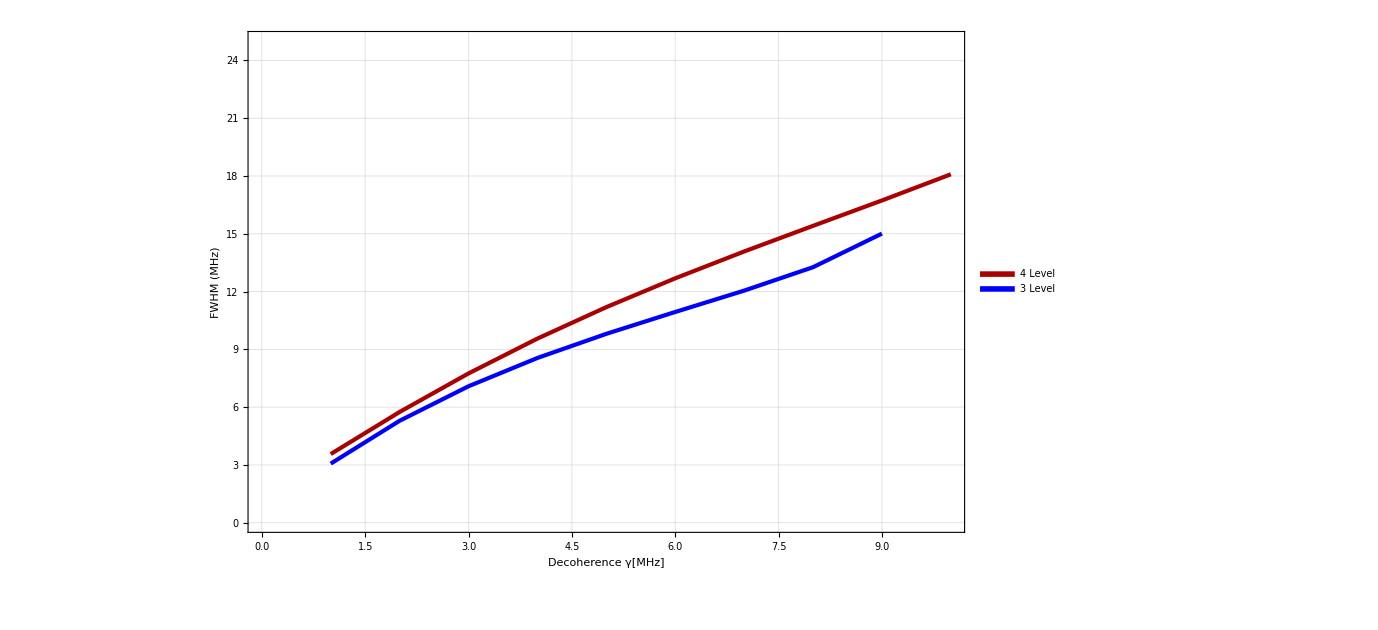

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,25}}]
```

p=5

```mathematica
Lev4DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.025,0.01,0.000002]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}]


]
```

```mathematica
Lev3DoppTestsc1[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.025,0.01,0.000002]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)

Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

General::ovfl: Overflow occurred in computation.

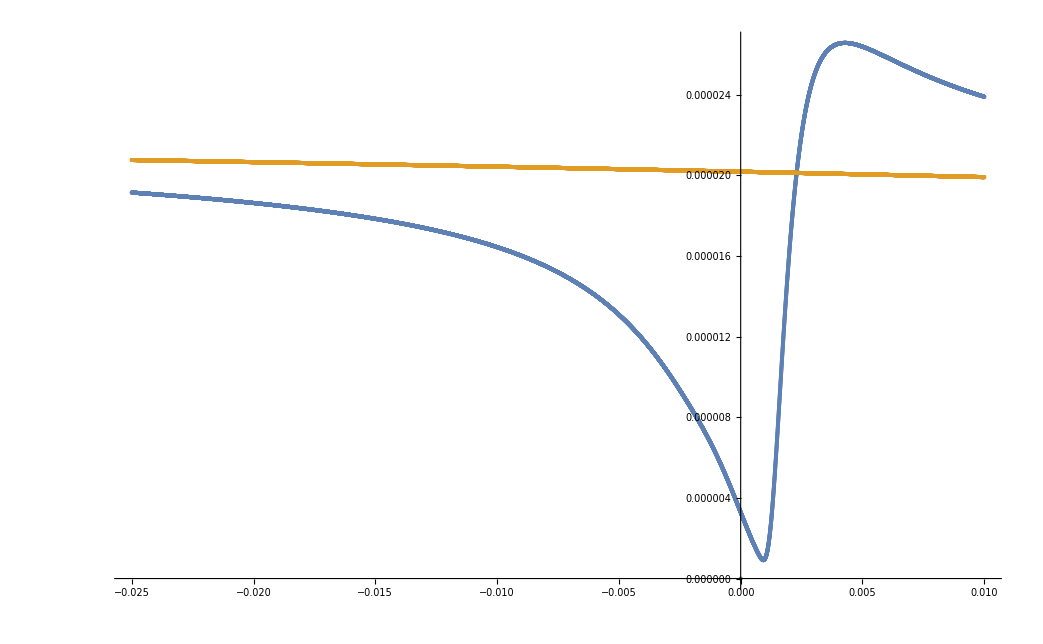

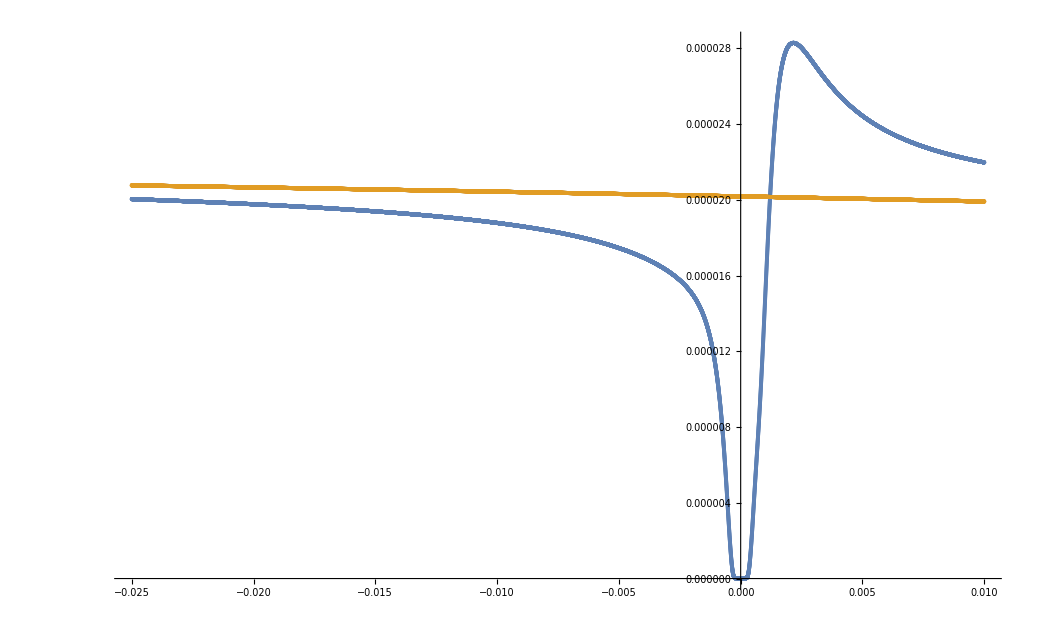

```mathematica
γ=0;
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
ListPlot[{list,list1},PlotRange->All]
ListPlot[{list3,list4},PlotRange->All]
```

```mathematica
p=15.8;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.0015&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.0015&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0.05,2.9,.05}]
]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::munfl: Exp[-816.644-2252.04 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-974.674-2283.02 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1143.62-2301.41 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
nf1=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Fvγ4[p]
nf2=Function[x,{ x[[1]]/( 5.750056),x[[2]]}]/@Fvγ3[p]
```

{{0.,4.565},{0.00869557,5.066},{0.0173911,5.267},{0.0260867,5.454},{0.0347823,5.631},{0.0434778,5.8},{0.0521734,5.961},{0.060869,6.119},{0.0695645,6.272},{0.0782601,6.422},{0.0869557,6.567},{0.0956512,6.712},{0.104347,6.852},{0.113042,6.991},{0.121738,7.128},{0.130434,7.263},{0.139129,7.397},{0.147825,7.528},{0.15652,7.658},{0.165216,7.787},{0.173911,7.917},{0.182607,8.043},{0.191302,8.17},{0.199998,8.294},{0.208694,8.418},{0.217389,8.541},{0.226085,8.663},{0.23478,8.785},{0.243476,8.905},{0.252171,9.026},{0.260867,9.146},{0.269563,9.265},{0.278258,9.383},{0.286954,9.5},{0.295649,9.617},{0.304345,9.734},{0.31304,9.85},{0.321736,9.966},{0.330432,10.081},{0.339127,10.197},{0.347823,10.311},{0.356518,10.425},{0.365214,10.539},{0.373909,10.651},{0.382605,10.764},{0.391301,10.877},{0.399996,10.989},{0.408692,11.1},{0.417387,11.211},{0.426083,11.322},{0.434778,11.433},{0.443474,11.542},{0.45217,11.654},{0.460865,11.762},{0.469561,11.873},{0.478256,11.981},{0.486952,12.09},{0.495647,12.198},{0.504343,12.306}}

```mathematica
nf2={{0.008695567486647087,1.7849999999999975},{0.017391134973294173,1.8549999999999978},{0.026086702459941262,1.9169999999999976},{0.03478226994658835,1.9849999999999977},{0.04347783743323543,2.058999999999998},{0.052173404919882524,2.136999999999998},{0.06086897240652961,2.218999999999998},{0.0695645398931767,2.306999999999998},{0.07826010737982378,2.3989999999999982},{0.08695567486647086,2.493999999999998},{0.09565124235311796,2.5919999999999987},{0.10434680983976505,2.695999999999999},{0.11304237732641213,2.800999999999998},{0.12173794481305922,2.910999999999999},{0.1304335122997063,3.022999999999998},{0.1391290797863534,3.1380000000000003},{0.1478246472730005,3.2559999999999985},{0.15652021475964756,3.3759999999999994},{0.16521578224629466,3.4989999999999997},{0.17391134973294173,3.623999999999999},{0.18260691721958883,3.7509999999999994},{0.19130248470623593,3.878999999999999},{0.199998052192883,4.007999999999999},{0.2086936196795301,4.139999999999999},{0.21738918716617717,4.2719999999999985},{0.22608475465282427,4.404999999999999},{0.23478032213947134,4.54},{0.24347588962611844,4.675999999999999},{0.25217145711276556,4.810999999999999},{0.2608670245994126,4.947},{0.2695625920860597,5.084},{0.2782581595727068,5.218999999999999},{0.28695372705935385,5.356},{0.295649294546001,5.494},{0.30434486203264804,5.63},{0.3130404295192951,5.7669999999999995},{0.3217359970059422,5.903000000000001},{0.3304315644925893,6.039000000000001},{0.3391271319792364,6.175},{0.34782269946588346,6.311000000000001},{0.3565182669525306,6.444999999999999},{0.36521383443917765,6.579999999999999},{0.3739094019258247,6.713999999999999},{0.38260496941247185,6.846999999999997},{0.39130053689911887,6.979999999999998},{0.399996104385766,7.1119999999999965},{0.40869167187241306,7.242999999999997},{0.4173872393590602,7.3729999999999976},{0.42608280684570726,7.503999999999999},{0.43477837433235433,7.633999999999998},{0.44347394181900146,7.761999999999997},{0.45216950930564853,7.889999999999998},{0.46086507679229566,8.015999999999998},{0.4695606442789427,8.142999999999999},{0.47825621176558974,8.267999999999997},{0.48695177925223687,8.391999999999998},{0.49564734673888394,8.516},{0.5043429142255311,8.638999999999998}}
```

{{0.00869557,1.785},{0.0173911,1.855},{0.0260867,1.917},{0.0347823,1.985},{0.0434778,2.059},{0.0521734,2.137},{0.060869,2.219},{0.0695645,2.307},{0.0782601,2.399},{0.0869557,2.494},{0.0956512,2.592},{0.104347,2.696},{0.113042,2.801},{0.121738,2.911},{0.130434,3.023},{0.139129,3.138},{0.147825,3.256},{0.15652,3.376},{0.165216,3.499},{0.173911,3.624},{0.182607,3.751},{0.191302,3.879},{0.199998,4.008},{0.208694,4.14},{0.217389,4.272},{0.226085,4.405},{0.23478,4.54},{0.243476,4.676},{0.252171,4.811},{0.260867,4.947},{0.269563,5.084},{0.278258,5.219},{0.286954,5.356},{0.295649,5.494},{0.304345,5.63},{0.31304,5.767},{0.321736,5.903},{0.330432,6.039},{0.339127,6.175},{0.347823,6.311},{0.356518,6.445},{0.365214,6.58},{0.373909,6.714},{0.382605,6.847},{0.391301,6.98},{0.399996,7.112},{0.408692,7.243},{0.417387,7.373},{0.426083,7.504},{0.434778,7.634},{0.443474,7.762},{0.45217,7.89},{0.460865,8.016},{0.469561,8.143},{0.478256,8.268},{0.486952,8.392},{0.495647,8.516},{0.504343,8.639}}

```mathematica
nf1={{0.008695567486647087,5.066},{0.017391134973294173,5.267},{0.026086702459941262,5.454000000000001},{0.03478226994658835,5.630999999999999},{0.04347783743323543,5.800000000000001},{0.052173404919882524,5.961},{0.06086897240652961,6.119000000000001},{0.0695645398931767,6.272},{0.07826010737982378,6.422000000000001},{0.08695567486647086,6.567000000000002},{0.09565124235311796,6.712000000000001},{0.10434680983976505,6.852},{0.11304237732641213,6.9910000000000005},{0.12173794481305922,7.128000000000001},{0.1304335122997063,7.263000000000001},{0.1391290797863534,7.397000000000001},{0.1478246472730005,7.527999999999998},{0.15652021475964756,7.657999999999998},{0.16521578224629466,7.786999999999997},{0.17391134973294173,7.916999999999999},{0.18260691721958883,8.042999999999997},{0.19130248470623593,8.169999999999998},{0.199998052192883,8.293999999999999},{0.2086936196795301,8.418},{0.21738918716617717,8.540999999999999},{0.22608475465282427,8.662999999999998},{0.23478032213947134,8.785},{0.24347588962611844,8.905},{0.25217145711276556,9.026},{0.2608670245994126,9.145999999999999},{0.2695625920860597,9.264999999999999},{0.2782581595727068,9.383},{0.28695372705935385,9.5},{0.295649294546001,9.616999999999999},{0.30434486203264804,9.734},{0.3130404295192951,9.85},{0.3217359970059422,9.966},{0.3304315644925893,10.081},{0.3391271319792364,10.196999999999997},{0.34782269946588346,10.310999999999998},{0.3565182669525306,10.425},{0.36521383443917765,10.539},{0.3739094019258247,10.651},{0.38260496941247185,10.764000000000001},{0.39130053689911887,10.876999999999999},{0.399996104385766,10.988999999999999},{0.40869167187241306,11.1},{0.4173872393590602,11.211},{0.42608280684570726,11.322},{0.43477837433235433,11.433},{0.44347394181900146,11.541999999999998},{0.45216950930564853,11.654000000000002},{0.46086507679229566,11.761999999999999},{0.4695606442789427,11.873000000000001},{0.47825621176558974,11.980999999999998},{0.48695177925223687,12.089999999999998},{0.49564734673888394,12.198},{0.5043429142255311,12.306}}
```

{{0.00869557,5.066},{0.0173911,5.267},{0.0260867,5.454},{0.0347823,5.631},{0.0434778,5.8},{0.0521734,5.961},{0.060869,6.119},{0.0695645,6.272},{0.0782601,6.422},{0.0869557,6.567},{0.0956512,6.712},{0.104347,6.852},{0.113042,6.991},{0.121738,7.128},{0.130434,7.263},{0.139129,7.397},{0.147825,7.528},{0.15652,7.658},{0.165216,7.787},{0.173911,7.917},{0.182607,8.043},{0.191302,8.17},{0.199998,8.294},{0.208694,8.418},{0.217389,8.541},{0.226085,8.663},{0.23478,8.785},{0.243476,8.905},{0.252171,9.026},{0.260867,9.146},{0.269563,9.265},{0.278258,9.383},{0.286954,9.5},{0.295649,9.617},{0.304345,9.734},{0.31304,9.85},{0.321736,9.966},{0.330432,10.081},{0.339127,10.197},{0.347823,10.311},{0.356518,10.425},{0.365214,10.539},{0.373909,10.651},{0.382605,10.764},{0.391301,10.877},{0.399996,10.989},{0.408692,11.1},{0.417387,11.211},{0.426083,11.322},{0.434778,11.433},{0.443474,11.542},{0.45217,11.654},{0.460865,11.762},{0.469561,11.873},{0.478256,11.981},{0.486952,12.09},{0.495647,12.198},{0.504343,12.306}}

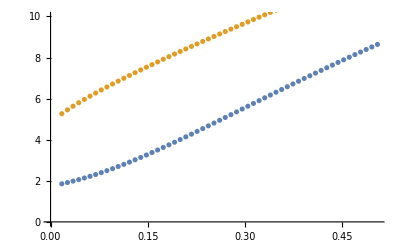

```mathematica
ListPlot[{nf2,nf1},PlotRange->{0,10}]
```

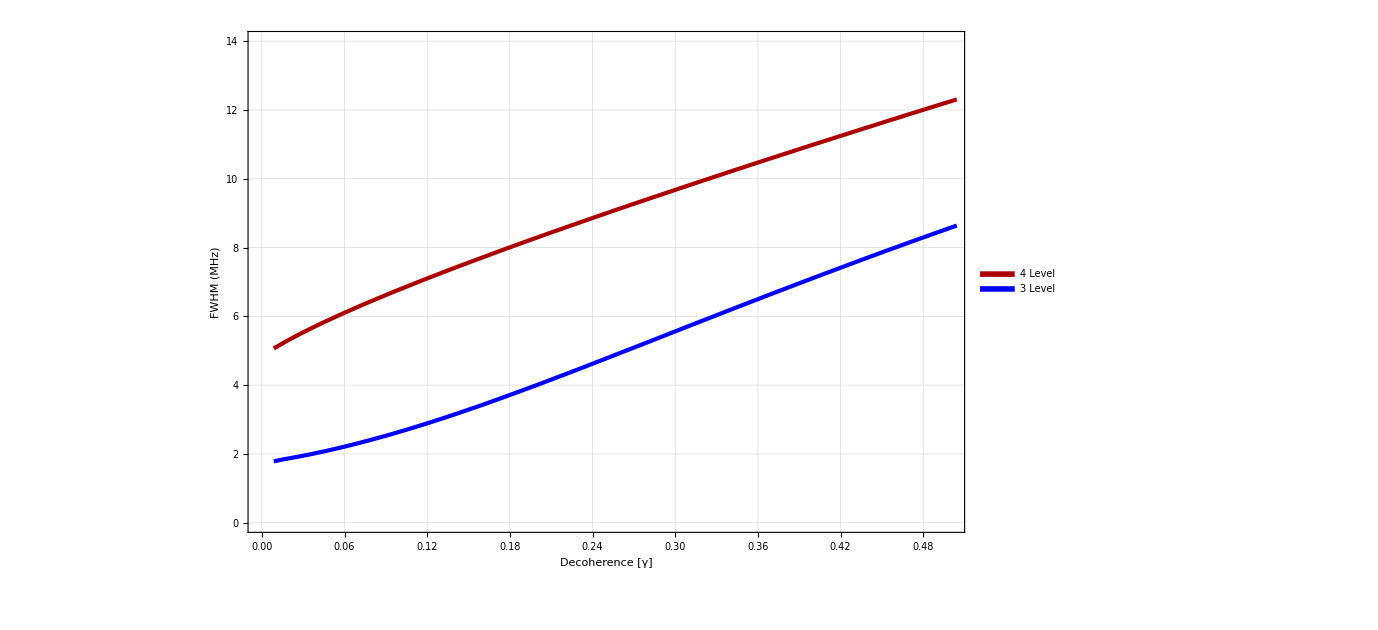

```mathematica
pd1=ListPlot[{nf1,nf2},PlotRange->{{0,.5},{0,14}},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.5}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence [γ]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure44U.eps",pd1]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure44U.eps

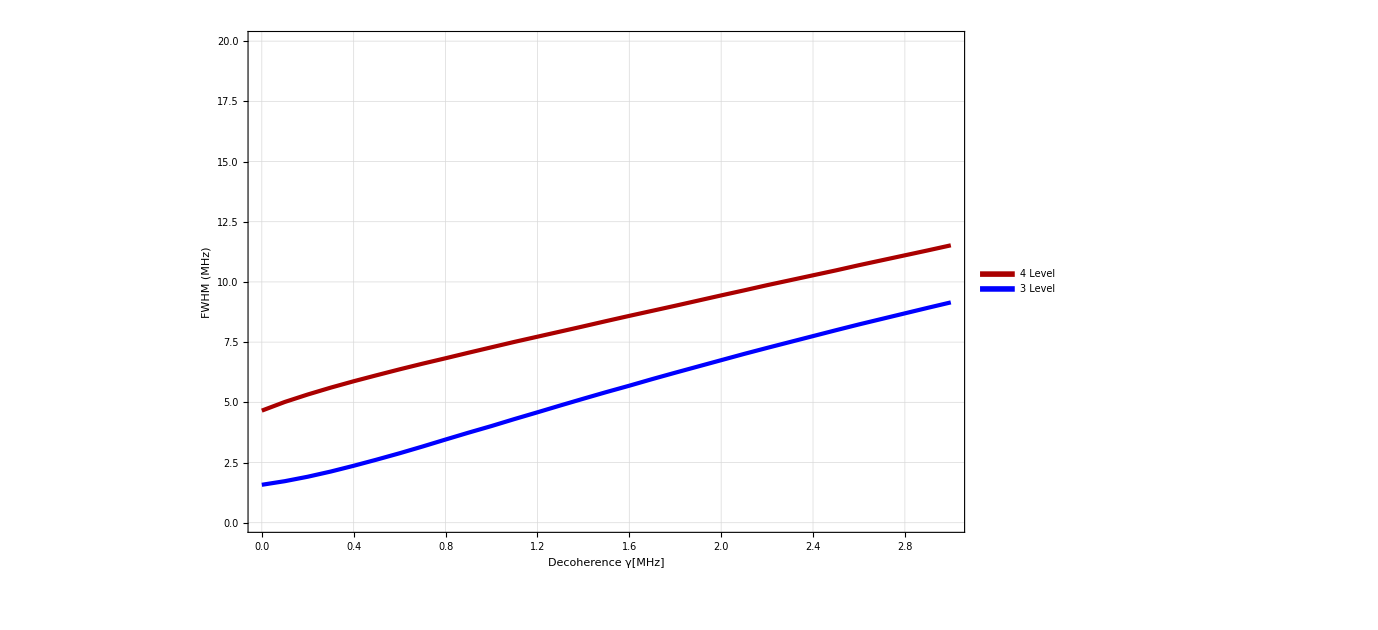

```mathematica
pd1=ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.8}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,3},{0,20}}]
```

p=10

```mathematica
p=65;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.005&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

```mathematica
.
```

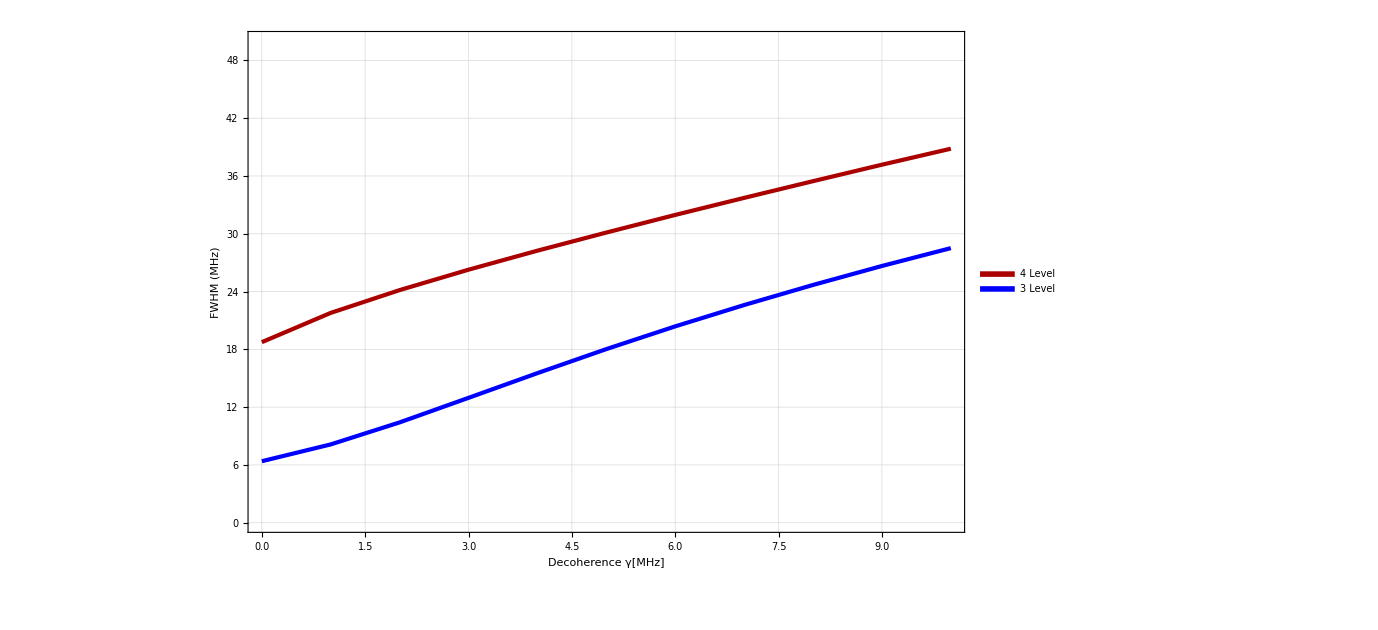

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,50}}]
```

p=15

```mathematica
p=145.75;
Fvγ4[p]={};Fvγ3[p]={};
Off[Power::infy];Off[Infinity::indet];

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1,LL,LL1,Midpoints,Midpoints1,cluster,cluster1},
Do[
list=Lev4DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list1=Lev4DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];
list3=Lev3DoppTestsc1[50,p/1000,1/1000,γ*10^6,0,0];
list4=Lev3DoppTestsc1[50,0/1000,1/1000,γ*10^6,0,0];

EIT=Min[DeleteCases[list[[All,2]],Indeterminate]];
ABS=list1[[Position[list,EIT][[1,1]]]][[2]];
EIT1=Min[DeleteCases[list3[[All,2]],Indeterminate]];
ABS1=list4[[Position[list3,EIT1][[1,1]]]][[2]];

LL=Abs[EIT-ABS];
Midpoints=Select[list,EIT+0.5(LL)-LL/50<#[[2]]<EIT+0.5(LL)+LL/50&];
cluster=Gather[Midpoints,Abs[#1[[1]]-#2[[1]]]<0.005&];
Fvγ4[p]=Append[Fvγ4[p],{γ,1000Abs[Mean[cluster[[1]][[All,1]]]-Mean[cluster[[2]][[All,1]]]]}];

LL1=Abs[EIT1-ABS1];
Midpoints1=Select[list3,EIT1+0.5(LL1)-LL1/50<#[[2]]<EIT1+0.5(LL1)+LL1/50&];
cluster1=Gather[Midpoints1,Abs[#1[[1]]-#2[[1]]]<0.003&];
Fvγ3[p]=Append[Fvγ3[p],{γ,1000Abs[Mean[cluster1[[1]][[All,1]]]-Mean[cluster1[[2]][[All,1]]]]}];
,{γ,0,10,1}]
]
```

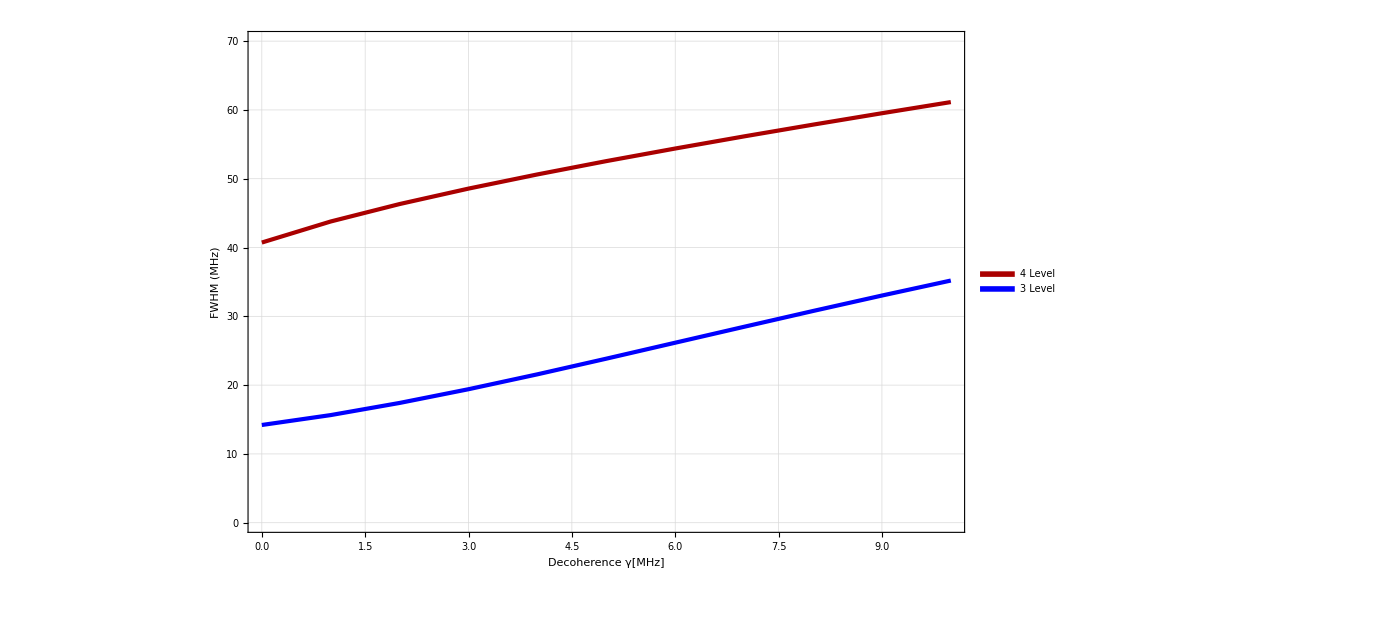

```mathematica
ListPlot[{Fvγ4[p],Fvγ3[p]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ[MHz]",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,70}}]
```

# Save

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\Final-Paper Figure"]
Export["Figure4TvP.eps",tp1]
Export["Figure4TvD.eps",td1]
Export["Figure4FvP.eps",Fp1]
Export["Figure4Fvd.eps",pd1]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\Final-Paper Figure

Figure4TvP.eps

Figure4TvD.eps

Figure4FvP.eps

Figure4Fvd.eps

```mathematica
pd1
```

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\2019-09-04 Final-Paper Figure"]
Export["Figure4TvD3.eps",td1]
Export["Figure4Fvd3.eps",pd1]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\2019-09-04 Final-Paper Figure

Figure4TvD3.eps

Figure4Fvd3.eps

```mathematica
tp1
```